# "Just Dance" (2008)

## Lady Gaga and Colby O'Donis

Arranged By Traci Johnson
Created April 3, 2010

```mathematica
-Graphics--Graphics-
```

"I was stuck in a ghetto La Quinta in the roughest part of Jacksonville, FL for three days with no internet. Going outside was not an option - there were drug deals going on in the parking lot and the cleaning lady was carrying around a bottle of tequila." - Traci Johnson (Version 1 Notes)

## Notes

This is the final draft of this spectacular tribute to perhaps the BEST Lady Gaga song of all time. I have fixed up the chorus and other miscellaneous mistakes and added some background "vocals," and to understand what I mean by that, you'll just have to see for yourself :)

You can check out the code by simply expanding the bracket on the right.

BTW, there's Ma-Ma-Ma-more Lady Gaga comin' attcha shortly...(I never get tired of that pun)

## Acknowledgements

### Lady Gaga, the new Queen of Pop - for writing this amazing song and being the best diva to ever hit the stage.

### Bill Titus - for all the Mathematica tutorials. I couldn't have written this working and well-formatted Mathematica notebook without them. F=ma, forever. (Sorry Bill, no frame and gridlines on this graphic).

### All the positive feedback about the first version. Thanks!

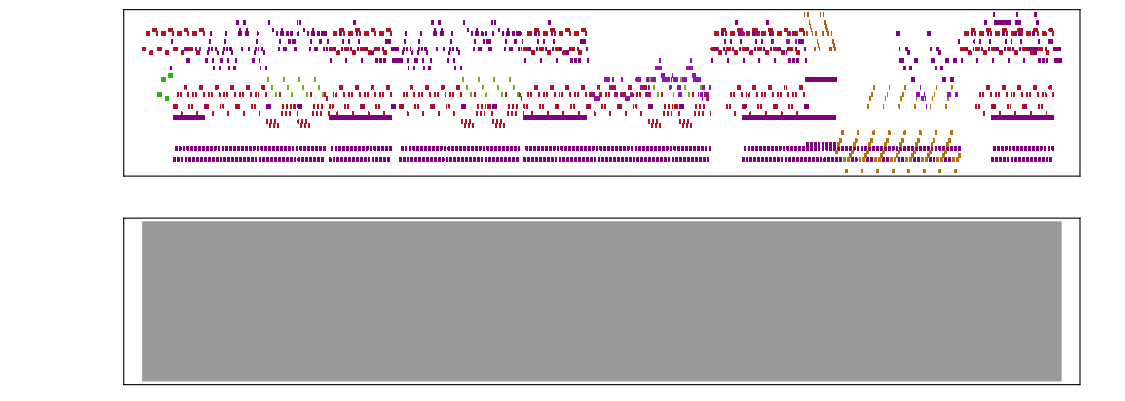

```mathematica
Sound[{

(* Introduction *)

SoundNote["E4",{0,0.25},"Polysynth",SoundVolume->3/4],
SoundNote["E4",{0.25,0.50},"Polysynth",SoundVolume->3/4],
SoundNote["E4",{0.50,0.75},"Polysynth",SoundVolume->3/4],
SoundNote["E4",{0.75,1.00},"Polysynth",SoundVolume->3/4],
SoundNote["G#4",{1.00,1.25},"Polysynth",SoundVolume->3/4],
SoundNote["G#4",{1.25,1.50},"Polysynth",SoundVolume->3/4],
SoundNote["G#4",{1.50,1.75},"Polysynth",SoundVolume->3/4],
SoundNote["G#4",{1.75,2.00},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{2.00,2.25},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{2.25,2.50},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{2.50,2.75},"Polysynth",SoundVolume->3/4],
SoundNote["A4",{2.75,3.00},"Polysynth",SoundVolume->3/4],
SoundNote["A4",{3.00,3.25},"Polysynth",SoundVolume->3/4],
SoundNote["A4",{3.25,3.50},"Polysynth",SoundVolume->3/4],
SoundNote["A4",{3.50,3.75},"Polysynth",SoundVolume->3/4],
SoundNote["G#4",{3.75,4.00},"Polysynth",SoundVolume->3/4],

SoundNote["E4",{4.00,4.25},"Polysynth",SoundVolume->3/4],SoundNote["E3",{3.95,5.00},"SynthStrings",SoundVolume->2],
SoundNote["E4",{4.25,4.50},"Polysynth",SoundVolume->3/4],
SoundNote["E4",{4.50,4.75},"Polysynth",SoundVolume->3/4],
SoundNote["E4",{4.75,5.00},"Polysynth",SoundVolume->3/4],
SoundNote["G#4",{5.00,5.25},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{4.95,6.00},"SynthStrings",SoundVolume->2],
SoundNote["G#4",{5.25,5.50},"Polysynth",SoundVolume->3/4],
SoundNote["G#4",{5.50,5.75},"Polysynth",SoundVolume->3/4],
SoundNote["G#4",{5.75,6.00},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{6.00,6.25},"Polysynth",SoundVolume->3/4],SoundNote["D#3",{5.95,6.75},"SynthStrings",SoundVolume->2],
SoundNote["D#4",{6.25,6.50},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{6.50,6.75},"Polysynth",SoundVolume->3/4],
SoundNote["A4",{6.75,7.00},"Polysynth",SoundVolume->3/4],SoundNote["A3",{6.70,7.75},"SynthStrings",SoundVolume->2],
SoundNote["A4",{7.00,7.25},"Polysynth",SoundVolume->3/4],
SoundNote["A4",{7.25,7.50},"Polysynth",SoundVolume->3/4],SoundNote["B3",{7.25,7.50},"Piano",SoundVolume->15],
SoundNote["A4",{7.50,7.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{7.50,7.75},"Piano",SoundVolume->15],
SoundNote["G#4",{7.75,8.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3","E4"},{8.00,8.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{8.00,8.50},"Piano",SoundVolume->15],SoundNote["BassDrum",{8.00,8.50}],SoundNote["HiHatOpen",{8.00,8.50}],SoundNote["CrashCymbal",{8.00,9.00}],
SoundNote["E4",{8.25,8.50},"Polysynth",SoundVolume->3/4],
SoundNote["E4",{8.50,8.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{8.50,9.00}],SoundNote["HiHatOpen",{8.50,9.00}],
SoundNote[{"C#3","E4"},{8.75,9.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"E3","G#4"},{9.00,9.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{9.00,9.50}],SoundNote["HiHatOpen",{9.00,9.50}],
SoundNote["G#4",{9.25,9.50},"Polysynth",SoundVolume->3/4],
SoundNote["G#4",{9.50,9.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{9.50,10.00}],SoundNote["HiHatOpen",{9.50,10.00}],
SoundNote[{"E3","G#4"},{9.75,10.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{10.00,10.25},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{10.00,10.75},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{10.00,10.50}],SoundNote["HiHatOpen",{10.00,10.50}],
SoundNote["D#4",{10.25,10.50},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{10.50,10.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{10.50,11.00}],SoundNote["HiHatOpen",{10.50,11.00}],
SoundNote[{"F#3","A4"},{10.75,11.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{10.75,11.00},"SlapBass",SoundVolume->3/4],
SoundNote["A4",{11.00,11.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{11.00,11.50}],SoundNote["HiHatOpen",{11.00,11.50}],
SoundNote[{"F#3","A4"},{11.25,11.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{11.25,11.50},"Piano",SoundVolume->15],
SoundNote["A4",{11.50,11.75},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{11.50,11.75},"Piano",SoundVolume->15],SoundNote["Snare",{11.50,12.00}],SoundNote["HiHatOpen",{11.50,12.00}],
SoundNote[{"E3","G#4"},{11.75,12.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{11.75,12.000},"Piano",SoundVolume->15],

SoundNote[{"C#3","E4"},{12.00,12.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{12.00,12.50}],SoundNote["HiHatOpen",{12.00,12.50}],SoundNote["C#4",{12.00,12.25},"Piano",SoundVolume->15],
SoundNote["E4",{12.25,12.50},"Polysynth",SoundVolume->3/4],
SoundNote["E4",{12.50,12.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{12.50,13.00}],SoundNote["HiHatOpen",{12.50,13.00}],
SoundNote[{"C#3","E4"},{12.75,13.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"E3","G#4"},{13.00,13.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{13.00,13.50}],SoundNote["HiHatOpen",{13.00,13.50}],
SoundNote["G#4",{13.25,13.50},"Polysynth",SoundVolume->3/4],
SoundNote["G#4",{13.50,13.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{13.50,14.00}],SoundNote["HiHatOpen",{13.50,14.00}],
SoundNote[{"E3","G#4"},{13.75,14.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{13.75,14.00},"SlapBass",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{14.00,14.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{14.00,14.50}],SoundNote["HiHatOpen",{14.00,14.50}],SoundNote["D#4",{14.00,14.25},"SlapBass",SoundVolume->1/2],
SoundNote["D#4",{14.25,14.50},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{14.50,14.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{14.50,15.00}],SoundNote["HiHatOpen",{14.50,15.00}],
SoundNote[{"F#3","A4"},{14.75,15.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{14.75,15.00},"SlapBass",SoundVolume->3/4],
SoundNote["A4",{15.00,15.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{15,15.50}],SoundNote["HiHatOpen",{15.00,15.50}],
SoundNote[{"F#3","A4"},{15.25,15.50},"Polysynth",SoundVolume->3/4],
SoundNote["A4",{15.50,15.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{15.50,16.00}],SoundNote["HiHatOpen",{15.50,16.00}],
SoundNote[{"E3","G#4"},{15.75,16.00},"Polysynth",SoundVolume->3/4],

(* Verse 1 *)

SoundNote[{"C#3"},{16.00,16.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{16.00,16.50}],SoundNote["CrashCymbal",{16.00,17.00}],
SoundNote[None,{16.25,16.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{16.25,16.50},"Piano"],
SoundNote[None,{16.50,16.75},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{16.50,16.75},"Piano"],SoundNote["Snare",{16.50,17.00}],
SoundNote[{"C#3"},{16.75,17.00},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{16.75,17.00},"Piano"],
SoundNote[{"E3"},{17.00,17.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{17.00,17.25},"Piano"],SoundNote["BassDrum",{17.00,17.50}],
SoundNote[None,{17.25,17.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{17.25,17.50},"Piano"],
SoundNote[None,{17.50,17.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{17.50,17.75},"Piano"],SoundNote["Snare",{17.50,18.00}],
SoundNote[{"E3"},{17.75,18.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{17.75,18.00},"Piano"],
SoundNote[{"B2"},{18.00,18.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{18.00,18.25},"Piano"],SoundNote["BassDrum",{18.00,18.50}],
SoundNote[None,{18.25,18.50},"Polysynth",SoundVolume->3/4],SoundNote["B3",{18.25,18.50},"Piano"],
SoundNote[None,{18.50,18.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{18.50,19.00}],
SoundNote[{"F#3"},{18.75,19.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{18.75,19.00},"Piano",SoundVolume->1/2],
SoundNote[None,{19.00,19.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{19.00,19.50}],
SoundNote[{"F#3"},{19.25,19.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{19.25,19.50},"Piano",SoundVolume->1/2],
SoundNote[None,{19.50,19.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{19.50,20.00}],
SoundNote[{"E3"},{19.75,20.00},"Polysynth",SoundVolume->3/4],SoundNote["B3",{19.75,20.00},"Piano",SoundVolume->1/2],

SoundNote[{"C#3"},{20.00,20.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{20.00,20.25},"Piano",SoundVolume->1/2],SoundNote["BassDrum",{20.00,20.50}],
SoundNote[None,{20.25,20.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{20.25,20.50},"Piano"],
SoundNote[None,{20.50,20.75},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{20.50,20.75},"Piano"],SoundNote["Snare",{20.50,21.00}],
SoundNote[{"C#3"},{20.75,21.00},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{20.75,21.00},"Piano"],
SoundNote[{"E3"},{21.00,21.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{21.00,21.25},"Piano"],SoundNote["BassDrum",{21.00,21.50}],
SoundNote[None,{21.25,21.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{21.25,21.50},"Piano"],
SoundNote[None,{21.50,21.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{21.50,21.75},"Piano"],SoundNote["Snare",{21.50,22.00}],
SoundNote[{"E3"},{21.75,22.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{21.75,22.00},"Piano"],
SoundNote[{"B2"},{22.00,22.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{22.00,22.25},"Piano"],SoundNote["BassDrum",{22.00,22.50}],
SoundNote[None,{22.25,22.50},"Polysynth",SoundVolume->3/4],SoundNote["B3",{22.25,22.50},"Piano"],
SoundNote[None,{22.50,22.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{22.50,22.75},"Piano",SoundVolume->1/2],SoundNote["Snare",{22.50,23.00}],
SoundNote[{"F#3"},{22.75,23.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{22.75,23.00},"Piano",SoundVolume->1/2],
SoundNote[None,{23.00,23.25},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{23.00,23.25},"Piano",SoundVolume->1/2],SoundNote["BassDrum",{23,23.50}],
SoundNote[{"F#3"},{23.25,23.50},"Polysynth",SoundVolume->3/4],
SoundNote[None,{23.50,23.75},"Polysynth",SoundVolume->3/4],SoundNote["B3",{23.50,24.00},"Piano",SoundVolume->1/2],SoundNote["Snare",{23.50,24.00}],
SoundNote[{"E3"},{23.75,24.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3"},{24.00,24.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{24.00,24.25},"Piano",SoundVolume->1/2],SoundNote["BassDrum",{24.00,24.50}],SoundNote["CrashCymbal",{24.00,25.00}],
SoundNote[None,{24.00,24.50},"Polysynth",SoundVolume->3/4],SoundNote["B4",{24.25,24.50},"Piano"],
SoundNote[None,{24.50,24.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{24.50,24.75},"Piano"],SoundNote["Snare",{24.50,25.00}],
SoundNote[{"C#3"},{24.75,25.00},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{24.75,25.00},"Piano"],
SoundNote[{"E3"},{25.00,25.25},"Polysynth",SoundVolume->3/4],SoundNote["A4",{25.00,25.25},"Piano"],SoundNote["BassDrum",{25.00,25.50}],
SoundNote[None,{25.25,25.50},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{25.25,25.50},"Piano"],
SoundNote[None,{25.50,25.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{25.50,25.75},"Piano"],SoundNote["Snare",{25.50,26.00}],
SoundNote[{"E3"},{25.75,26.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{25.75,26.00},"Piano"],
SoundNote[{"B2"},{26.00,26.25},"Polysynth",SoundVolume->3/4],SoundNote["B4",{26.00,26.25},"Piano"],SoundNote["BassDrum",{26.00,26.50}],
SoundNote[None,{26.25,26.50},"Polysynth",SoundVolume->3/4],SoundNote["B4",{26.25,26.50},"Piano"],
SoundNote[None,{26.50,26.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{26.50,26.75},"Piano"],SoundNote["Snare",{26.50,27.00}],
SoundNote[{"F#3"},{26.75,27.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{26.75,27.00},"Piano"],
SoundNote[None,{27.00,27.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{27.00,27.25},"Piano"],SoundNote["BassDrum",{27.00,27.50}],
SoundNote[{"F#3"},{27.25,27.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{27.25,27.50},"Piano"],
SoundNote[None,{27.50,27.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{27.50,28.00}],
SoundNote[{"E3"},{27.75,28.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3"},{28.00,28.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{28.00,28.50}],
SoundNote[None,{28.25,28.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{28.25,28.50},"Piano"],
SoundNote[None,{28.50,28.75},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{28.50,28.75},"Piano"],SoundNote["Snare",{28.50,29.00}],
SoundNote[{"C#3"},{28.75,29.00},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{28.75,29.00},"Piano"],
SoundNote[{"E3"},{29.00,29.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{29.00,29.25},"Piano"],SoundNote["BassDrum",{29.00,29.50}],
SoundNote[None,{29.25,29.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{29.25,29.50},"Piano"],
SoundNote[None,{29.50,29.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{29.50,29.75},"Piano"],SoundNote["Snare",{29.50,30.00}],
SoundNote[{"E3"},{29.75,30.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{29.75,30.00},"Piano"],
SoundNote[{"B2"},{30.00,30.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{30.00,30.25},"Piano"],SoundNote["BassDrum",{30.00,30.50}],
SoundNote[None,{30.25,30.50},"Polysynth",SoundVolume->3/4],SoundNote["B3",{30.25,30.50},"Piano"],
SoundNote[None,{30.50,30.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{30.50,31.00}],
SoundNote[{"F#3"},{30.75,31.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{30.75,31.00},"Piano",SoundVolume->1/2],
SoundNote[None,{31.00,31.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{31.00,31.50}],
SoundNote[{"F#3"},{31.25,31.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{31.25,31.50},"Piano",SoundVolume->1/2],
SoundNote[None,{31.50,31.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{31.50,32.00}],
SoundNote[{"E3"},{31.75,32.00},"Polysynth",SoundVolume->3/4],SoundNote["B3",{31.75,32.00},"Piano",SoundVolume->1/2],

(* Prechorus 1 *)

SoundNote["A2",{32.00,32.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{32.00,32.50}],SoundNote["CrashCymbal",{32.00,33.00}],
SoundNote["G#3",{32.25,32.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{32.25,32.50},"Piano"],
SoundNote[None,{32.50,32.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{32.50,32.75},"Piano"],SoundNote["Snare",{32.50,33.00}],
SoundNote["G#2",{32.75,33.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{32.75,33.00},"Piano"],
SoundNote["A2",{33.00,33.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{33.00,33.25},"Piano"],SoundNote["BassDrum",{33.00,33.50}],
SoundNote["F#3",{33.25,33.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{33.25,33.50},"Piano"],
SoundNote[None,{33.50,33.75},"Polysynth",SoundVolume->3/4],SoundNote["A4",{33.50,33.75},"Piano"],SoundNote["Snare",{33.50,34.00}],
SoundNote["G#2",{33.75,34.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{33.75,34.00},"Piano"],
SoundNote["A2",{34.00,34.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{34.00,34.25},"Piano"],SoundNote["BassDrum",{34.00,34.50}],
SoundNote["E3",{34.25,34.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{34.25,34.50},"Piano"],
SoundNote[None,{34.50,34.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{34.50,34.75},"Piano"],SoundNote["Snare",{34.50,35.00}],
SoundNote["G#2",{34.75,35.00},"Polysynth",SoundVolume->3/4],
SoundNote[None,{35.00,35.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{35.00,35.25},"Piano"],SoundNote["BassDrum",{35.00,35.50}],
SoundNote["E3",{35.25,35.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{35.25,35.50},"Piano"],
SoundNote[None,{35.50,35.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{35.50,35.75},"Piano"],SoundNote["Snare",{35.50,36.00}],
SoundNote["B2",{35.75,36.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{35.75,36.00},"Piano"],

SoundNote["C#3",{36.00,36.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{36.00,36.25},"Piano"],SoundNote["BassDrum",{36.00,36.50}],
SoundNote["G#3",{36.25,36.50},"SteelGuitar",SoundVolume->3/4],SoundNote["E4",{36.25,36.50},"Piano"],
SoundNote[None,{36.50,36.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{36.50,36.75},"Piano"],SoundNote["Snare",{36.50,37.00}],
SoundNote["B2",{36.75,37.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{36.75,37.00},"Piano"],
SoundNote["C#3",{37.00,37.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{37.00,37.25},"Piano"],SoundNote["BassDrum",{37.00,37.50}],
SoundNote["F#3",{37.25,37.50},"SteelGuitar",SoundVolume->3/4],SoundNote["G#4",{37.25,37.50},"Piano"],
SoundNote[None,{37.50,37.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{37.50,37.75},"Piano"],SoundNote["Snare",{37.50,38.00}],
SoundNote["B2",{37.75,38.00},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{37.75,38.00},"Piano"],
SoundNote["C#3",{38.00,38.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{38.00,38.25},"Piano"],SoundNote["BassDrum",{38.00,38.50}],
SoundNote["E3",{38.25,38.50},"SteelGuitar",SoundVolume->3/4],SoundNote["G#4",{38.25,38.50},"Piano"],
SoundNote[None,{38.50,38.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{38.50,38.75},"Piano"],SoundNote["Snare",{38.50,39.00}],
SoundNote["C#3",{38.75,39.00},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{38.75,39.00},"Piano"],
SoundNote[None,{39.00,39.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{39.00,39.25},"Piano"],SoundNote["BassDrum",{39.00,39.50}],
SoundNote["C#3",{39.25,39.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{39.25,39.50},"Piano"],
SoundNote[None,{39.50,39.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{39.50,39.75},"Piano"],SoundNote["Snare",{39.50,40.00}],
SoundNote["B2",{39.75,40.00},"Polysynth",SoundVolume->3/4],SoundNote["B4",{39.75,40.00},"Piano"],

SoundNote["A2",{40.00,40.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{40.00,40.25},"Piano"],SoundNote["BassDrum",{40.00,40.50}],SoundNote["CrashCymbal",{40.00,41.00}],
SoundNote["G#3",{40.25,40.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{40.25,40.50},"Piano"],
SoundNote[None,{40.50,40.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{40.50,40.75},"Piano"],SoundNote["Snare",{40.50,41.00}],
SoundNote["G#2",{40.75,41.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{40.75,41.00},"Piano"],
SoundNote["A2",{41.00,41.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{41.00,41.25},"Piano"],SoundNote["BassDrum",{41.00,41.50}],
SoundNote["F#3",{41.25,41.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{41.25,41.50},"Piano"],
SoundNote[None,{41.50,41.75},"Polysynth",SoundVolume->3/4],SoundNote["A4",{41.50,41.75},"Piano"],SoundNote["Snare",{41.50,42.00}],
SoundNote["G#2",{41.75,42.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{41.75,42.00},"Piano"],
SoundNote["A2",{42.00,42.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{42.00,42.25},"Piano"],SoundNote["BassDrum",{42.00,42.50}],
SoundNote["E3",{42.25,42.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{42.25,42.50},"Piano"],
SoundNote[None,{42.50,42.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{42.50,42.75},"Piano"],SoundNote["Snare",{42.50,43.00}],
SoundNote["G#2",{42.75,43.00},"Polysynth",SoundVolume->3/4],
SoundNote[None,{43.00,43.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{43.00,43.25},"Piano"],SoundNote["BassDrum",{43.00,43.50}],
SoundNote["E3",{43.25,43.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{43.25,43.50},"Piano"],
SoundNote[None,{43.50,43.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{43.50,43.75},"Piano"],SoundNote["Snare",{43.50,44.00}],
SoundNote["B2",{43.75,44.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{43.75,44.00},"Piano"],

SoundNote["C#3",{44.00,44.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{44.00,44.25},"Piano"],SoundNote["BassDrum",{44.00,44.50}],
SoundNote["G#3",{44.25,44.50},"SteelGuitar",SoundVolume->3/4],SoundNote["E4",{44.25,44.50},"Piano"],
SoundNote[None,{44.50,44.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{44.50,44.75},"Piano"],SoundNote["Snare",{44.50,45.00}],
SoundNote["B2",{44.75,45.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{44.75,45.00},"Piano"],
SoundNote["C#3",{45.00,45.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{45.00,45.25},"Piano"],SoundNote["BassDrum",{45.00,45.50}],
SoundNote["F#3",{45.25,45.50},"SteelGuitar",SoundVolume->3/4],SoundNote["G#4",{45.25,45.50},"Piano"],
SoundNote[None,{45.50,45.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{45.50,45.75},"Piano"],SoundNote["Snare",{45.50,46.00}],
SoundNote["B2",{45.75,46.00},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{45.75,46.00},"Piano"],
SoundNote["C#3",{46.00,46.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{46.00,46.25},"Piano"],SoundNote["BassDrum",{46.00,46.50}],
SoundNote["E3",{46.25,46.50},"SteelGuitar",SoundVolume->3/4],SoundNote["G#4",{46.25,46.50},"Piano"],
SoundNote[None,{46.50,46.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{46.50,46.75},"Piano"],SoundNote["Snare",{46.50,47.00}],
SoundNote["E3",{46.75,47.00},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{46.75,47.00},"Piano"],
SoundNote[None,{47.00,47.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{47.00,47.25},"Piano"],
SoundNote["D#3",{47.25,47.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{47.25,47.50},"Piano"],
SoundNote[None,{47.50,47.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{47.50,47.75},"Piano"],
SoundNote["B2",{47.75,48.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{47.75,48.00},"Piano"],

(* Chorus 1 *)

SoundNote[{"C#3","E4"},{48.00,48.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{48.00,48.25},"Piano"],SoundNote["BassDrum",{48.00,48.50}],SoundNote["HiHatOpen",{48.00,48.50}],SoundNote["CrashCymbal",{48.00,48.25}],
SoundNote["E4",{48.25,48.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{48.25,48.50},"Piano"],
SoundNote["E4",{48.50,48.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{48.50,49.00}],SoundNote["HiHatOpen",{48.50,49.00}],
SoundNote[{"C#3","E4"},{48.75,49.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{48.75,49.00},"Piano"],
SoundNote[{"E3","G#4"},{49.00,49.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{49.00,49.25},"Piano"],SoundNote["BassDrum",{49.00,49.50}],SoundNote["HiHatOpen",{49.00,49.50}],
SoundNote["G#4",{49.25,49.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{49.25,49.50},"Piano"],
SoundNote["G#4",{49.50,49.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{49.50,49.75},"Piano"],SoundNote["Snare",{49.50,50.00}],SoundNote["HiHatOpen",{49.50,50.00}],
SoundNote[{"E3","G#4"},{49.75,50.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{50.00,50.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{50.00,50.50}],SoundNote["HiHatOpen",{50.00,50.50}],
SoundNote["D#4",{50.25,50.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{50.25,50.50},"Piano"],
SoundNote["D#4",{50.50,50.75},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{50.50,50.75},"Piano"],SoundNote["Snare",{50.50,51.00}],SoundNote["HiHatOpen",{50.50,51.00}],
SoundNote[{"F#3","A4"},{50.75,51.00},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{50.75,51.00},"Piano"],
SoundNote["A4",{51.00,51.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{51.00,51.25},"Piano"],SoundNote["BassDrum",{51.00,51.50}],SoundNote["HiHatOpen",{51.00,51.50}],
SoundNote[{"F#3","A4"},{51.25,51.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{51.25,51.50},"Piano"],
SoundNote["A4",{51.50,51.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{51.50,51.75},"Piano"],SoundNote["Snare",{51.50,52.00}],SoundNote["HiHatOpen",{51.50,52.00}],
SoundNote[{"E3","G#4"},{51.75,52.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3","E4"},{52.00,52.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{52.00,52.25},"Piano"],SoundNote["BassDrum",{52.00,52.50}],SoundNote["HiHatOpen",{52.00,52.50}],
SoundNote["E4",{52.25,52.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{52.25,52.50},"Piano"],
SoundNote["E4",{52.50,52.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{52.50,52.75},"Piano"],SoundNote["Snare",{52.50,53.00}],SoundNote["HiHatOpen",{52.50,53.00}],
SoundNote[{"C#3","E4"},{52.75,53.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{52.75,53.00},"Piano"],
SoundNote[{"E3","G#4"},{53.00,53.25},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{53.00,53.25},"Piano"],SoundNote["BassDrum",{53.00,53.50}],SoundNote["HiHatOpen",{53.00,53.50}],
SoundNote["G#4",{53.25,53.50},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{53.25,53.50},"Piano"],
SoundNote["G#4",{53.50,53.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{53.50,53.75},"Piano"],SoundNote["Snare",{53.50,54.00}],SoundNote["HiHatOpen",{53.50,54.00}],
SoundNote[{"E3","G#4"},{53.75,54.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{54.00,54.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{54.00,54.50}],SoundNote["HiHatOpen",{54.00,54.50}],
SoundNote["D#4",{54.25,54.50},"Polysynth",SoundVolume->3/4],SoundNote["B4",{54.25,54.50},"Piano"],
SoundNote["D#4",{54.50,54.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{54.50,54.75},"Piano"],SoundNote["Snare",{54.50,55.00}],SoundNote["HiHatOpen",{54.50,55.00}],
SoundNote[{"F#3","A4"},{54.75,55.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{54.75,55.00},"Piano"],
SoundNote["A4",{55.00,55.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{55.00,55.25},"Piano"],SoundNote["BassDrum",{55.00,55.50}],SoundNote["HiHatOpen",{55.00,55.50}],
SoundNote[{"F#3","A4"},{55.25,55.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{55.25,55.50},"Piano"],
SoundNote["A4",{55.50,55.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{55.50,55.75},"Piano"],SoundNote["Snare",{55.50,56.00}],SoundNote["HiHatOpen",{55.50,56.00}],
SoundNote[{"E3","G#4"},{55.75,56.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3","E4"},{56.00,56.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{56.00,56.25},"Piano"],SoundNote["BassDrum",{56.00,56.50}],SoundNote["HiHatOpen",{56.00,56.50}],SoundNote["CrashCymbal",{56.00,57.00}],
SoundNote["E4",{56.25,56.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{56.25,56.50},"Piano"],
SoundNote["E4",{56.50,56.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{56.50,57.00}],SoundNote["HiHatOpen",{56.50,57.00}],
SoundNote[{"C#3","E4"},{56.75,57.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{56.75,57.00},"Piano"],
SoundNote[{"E3","G#4"},{57.00,57.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{57.00,57.25},"Piano"],SoundNote["BassDrum",{57.00,57.50}],SoundNote["HiHatOpen",{57.00,57.50}],
SoundNote["G#4",{57.25,57.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{57.25,57.50},"Piano"],
SoundNote["G#4",{57.50,57.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{57.50,57.75},"Piano"],SoundNote["Snare",{57.50,58.00}],SoundNote["HiHatOpen",{57.50,58.00}],
SoundNote[{"E3","G#4"},{57.75,58.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{58.00,58.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{58.00,58.50}],SoundNote["HiHatOpen",{58.00,58.50}],
SoundNote["D#4",{58.25,58.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{58.25,58.50},"Piano"],
SoundNote["D#4",{58.50,58.75},"Polysynth",SoundVolume->3/4],SoundNote[None,{58.50,58.75},"Piano"],SoundNote["Snare",{58.50,59}],SoundNote["HiHatOpen",{58.50,59.00}],
SoundNote[{"F#3","A4"},{58.75,59.00},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{58.75,59.00},"Piano"],
SoundNote["A4",{59.00,59.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{59.00,59.25},"Piano"],SoundNote["BassDrum",{59.00,59.50}],SoundNote["HiHatOpen",{59.00,59.50}],
SoundNote[{"F#3","A4"},{59.25,59.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{59.25,59.50},"Piano"],
SoundNote["A4",{59.50,59.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{59.50,60.00}],SoundNote["HiHatOpen",{59.50,60.00}],
SoundNote[{"E3","G#4"},{59.75,60.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{59.75,60.00},"Piano"],

SoundNote[{"C#3","E4"},{60.00,60.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{60.00,60.50},"Piano"],SoundNote["BassDrum",{60.00,60.50}],SoundNote["HiHatOpen",{60.00,60.50}],
SoundNote["E4",{60.25,60.50},"Polysynth",SoundVolume->3/4],
SoundNote["E4",{60.50,60.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{60.50,61.00}],SoundNote["HiHatOpen",{60.50,62.00}],
SoundNote[{"C#3","E4"},{60.75,61.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{60.75,61.00},"Piano"],
SoundNote[{"E3","G#4"},{61.00,61.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{61.00,61.50},"Piano"],SoundNote["BassDrum",{61.00,61.50}],SoundNote["HiHatOpen",{61.00,61.50}],
SoundNote["G#4",{61.25,61.50},"Polysynth",SoundVolume->3/4],SoundNote[None,{61.25,61.50},"Piano"],
SoundNote["G#4",{61.50,61.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{61.50,62.00}],SoundNote["HiHatOpen",{61.50,62.00}],
SoundNote[{"E3","G#4"},{61.75,62.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{61.75,62.00},"Piano"],
SoundNote[{"B2","D#4"},{62.00,62.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{62.00,62.50},"Piano"],SoundNote["BassDrum",{62.00,62.50}],SoundNote["HiHatOpen",{62.00,62.50}],
SoundNote["D#4",{62.25,62.50},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{62.50,62.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{62.50,62.75},"Piano"],SoundNote["Snare",{62.50,63.00}],SoundNote["HiHatOpen",{62.50,63.00}],
SoundNote[{"F#3","A4"},{62.75,63.00},"Polysynth",SoundVolume->3/4],
SoundNote["A4",{63.00,63.25},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{63.00,63.25},"Piano"],SoundNote["BassDrum",{63.00,63.50}],SoundNote["HiHatOpen",{63.00,63.50}],
SoundNote[{"F#3","A4"},{63.25,63.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{63.25,63.50},"Piano"],
SoundNote["A4",{63.50,63.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{63.50,63.75},"Piano"],SoundNote["Snare",{63.50,64.00}],SoundNote["HiHatOpen",{63.50,64.00}],
SoundNote[{"E3","G#4"},{63.75,64.00},"Polysynth",SoundVolume->3/4],

SoundNote["E4",{64.00,64.25},"Piano"],SoundNote["C#4",{64.25,64.50},"Piano"],SoundNote["CrashCymbal",{64.00,65.00}],
SoundNote["E4",{64.50,64.75},"Piano",SoundVolume->1/4],SoundNote["C#4",{64.75,65.00},"Piano",SoundVolume->1/4],
SoundNote["E4",{65.00,65.25},"Piano",SoundVolume->1/8],SoundNote["C#4",{65.25,65.50},"Piano",SoundVolume->1/8],
SoundNote["E4",{65.50,65.75},"Piano",SoundVolume->1/16],SoundNote["C#4",{65.75,66.00},"Piano",SoundVolume->1/16],

(* Verse 2 *)

SoundNote[{"C#3"},{66.00,66.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{66.00,66.50}],SoundNote["CrashCymbal",{66.00,67.00}],
SoundNote[None,{66.25,66.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{66.25,66.50},"Piano"],
SoundNote[None,{66.50,66.75},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{66.50,66.75},"Piano"],SoundNote["Snare",{66.50,67.00}],
SoundNote[{"C#3"},{66.75,67.00},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{66.75,67.00},"Piano"],
SoundNote[{"E3"},{67.00,67.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{67.00,67.25},"Piano"],SoundNote["BassDrum",{67.00,67.50}],
SoundNote[None,{67.25,67.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{67.25,67.50},"Piano"],
SoundNote[None,{67.50,67.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{67.50,67.75},"Piano"],SoundNote["Snare",{67.50,68.00}],
SoundNote[{"E3"},{67.75,68.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{67.75,68.00},"Piano"],
SoundNote[{"B2"},{68.00,68.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{68.00,68.25},"Piano"],SoundNote["BassDrum",{68.00,68.50}],
SoundNote[None,{68.25,68.50},"Polysynth",SoundVolume->3/4],SoundNote["B3",{68.25,68.50},"Piano"],
SoundNote[None,{68.50,68.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{68.50,69.00}],
SoundNote[{"F#3"},{68.75,69.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{68.75,69.00},"Piano",SoundVolume->1/2],
SoundNote[None,{69.00,69.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{69.00,69.50}],
SoundNote[{"F#3"},{69.25,69.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{69.25,69.50},"Piano",SoundVolume->1/2],
SoundNote[None,{69.50,69.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{69.50,70.00}],
SoundNote[{"E3"},{69.75,70.00},"Polysynth",SoundVolume->3/4],SoundNote["B3",{69.75,70.00},"Piano",SoundVolume->1/2],

SoundNote[{"C#3"},{70.00,70.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{70.00,70.25},"Piano",SoundVolume->1/2],SoundNote["BassDrum",{70.00,70.50}],
SoundNote[None,{70.25,70.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{70.25,70.50},"Piano"],
SoundNote[None,{70.50,70.75},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{70.50,70.75},"Piano"],SoundNote["Snare",{70.50,71.00}],
SoundNote[{"C#3"},{70.75,71.00},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{70.75,71.00},"Piano"],
SoundNote[{"E3"},{71.00,71.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{71.00,71.25},"Piano"],SoundNote["BassDrum",{71.00,71.50}],
SoundNote[None,{71.25,71.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{71.25,71},"Piano"],
SoundNote[None,{71.50,71.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{71.50,71.75},"Piano"],SoundNote["Snare",{71.50,72.00}],
SoundNote[{"E3"},{71.75,72.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{71.75,72.00},"Piano"],
SoundNote[{"B2"},{72.00,72.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{72.00,72.25},"Piano"],SoundNote["BassDrum",{72.00,72.50}],
SoundNote[None,{72.25,72.50},"Polysynth",SoundVolume->3/4],SoundNote["B3",{72.25,72.50},"Piano"],
SoundNote[None,{72.50,72.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{72.50,72.75},"Piano",SoundVolume->1/2],SoundNote["Snare",{72.50,73.00}],
SoundNote[{"F#3"},{72.75,73.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{72.75,73.00},"Piano",SoundVolume->1/2],
SoundNote[None,{73.00,73.25},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{73.00,73.25},"Piano",SoundVolume->1/2],SoundNote["BassDrum",{73.00,73.50}],
SoundNote[{"F#3"},{73.25,73.50},"Polysynth",SoundVolume->3/4],
SoundNote[None,{73.50,73.75},"Polysynth",SoundVolume->3/4],SoundNote["B3",{73.50,74.00},"Piano",SoundVolume->1/2],SoundNote["Snare",{73.50,74.00}],
SoundNote[{"E3"},{73.75,74.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3"},{74.00,74.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{74.00,74.25},"Piano",SoundVolume->1/2],SoundNote["BassDrum",{74.00,74.50}],SoundNote["CrashCymbal",{74.00,75.00}],
SoundNote[None,{74.00,74.50},"Polysynth",SoundVolume->3/4],SoundNote["B4",{74.25,74.50},"Piano"],
SoundNote[None,{74.50,74.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{74.50,74.75},"Piano"],SoundNote["Snare",{74.50,75.00}],
SoundNote[{"C#3"},{74.75,75.00},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{74.75,75.00},"Piano"],
SoundNote[{"E3"},{75.00,75.25},"Polysynth",SoundVolume->3/4],SoundNote["A4",{75.00,75.25},"Piano"],SoundNote["BassDrum",{75.00,75.50}],
SoundNote[None,{75.25,75.50},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{75.25,75.50},"Piano"],
SoundNote[None,{75.50,75.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{75.50,75.75},"Piano"],SoundNote["Snare",{75.50,76.00}],
SoundNote[{"E3"},{75.75,76.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{75.75,76.00},"Piano"],
SoundNote[{"B2"},{76.00,76.25},"Polysynth",SoundVolume->3/4],SoundNote["B4",{76.00,76.25},"Piano"],SoundNote["BassDrum",{76.00,76.50}],
SoundNote[None,{76.25,76.50},"Polysynth",SoundVolume->3/4],SoundNote["B4",{76.25,76.50},"Piano"],
SoundNote[None,{76.50,76.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{76.50,76.75},"Piano"],SoundNote["Snare",{76.50,77.00}],
SoundNote[{"F#3"},{76.75,77.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{76.75,77.00},"Piano"],
SoundNote[None,{77.00,77.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{77.00,77.25},"Piano"],SoundNote["BassDrum",{77.00,77.50}],
SoundNote[{"F#3"},{77.25,77.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{77.25,77.50},"Piano"],
SoundNote[None,{77.50,77.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{77.50,78.00}],
SoundNote[{"E3"},{77.75,78.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3"},{78.00,78.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{78.00,78.50}],
SoundNote[None,{78.25,78.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{78.25,78.50},"Piano"],
SoundNote[None,{78.50,78.75},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{78.50,78.75},"Piano"],SoundNote["Snare",{78.50,79.00}],
SoundNote[{"C#3"},{78.75,79.00},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{78.75,79.00},"Piano"],
SoundNote[{"E3"},{79.00,79.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{79.00,79.25},"Piano"],SoundNote["BassDrum",{79.00,79.50}],
SoundNote[None,{79.25,79.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{79.25,79.50},"Piano"],
SoundNote[None,{79.50,79.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{79.50,79.75},"Piano"],SoundNote["Snare",{79.50,80.00}],
SoundNote[{"E3"},{79.75,80.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{79.75,80.00},"Piano"],
SoundNote[{"B2"},{80.00,80.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{80.00,80.25},"Piano"],SoundNote["BassDrum",{80.00,80.50}],
SoundNote[None,{80.25,80.50},"Polysynth",SoundVolume->3/4],SoundNote["B3",{80.25,80.50},"Piano"],
SoundNote[None,{80.50,80.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{80.50,81.00}],
SoundNote[{"F#3"},{80.75,81.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{80.75,81.00},"Piano",SoundVolume->1/2],
SoundNote[None,{81.00,81.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{81.00,81.50}],
SoundNote[{"F#3"},{81.25,81.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{81.25,81.50},"Piano",SoundVolume->1/2],
SoundNote[None,{81.50,81.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{81.50,82.00}],
SoundNote[{"E3"},{81.75,82.00},"Polysynth",SoundVolume->3/4],SoundNote["B3",{81.75,82.00},"Piano",SoundVolume->1/2],

(* Prechorus 2 *)

SoundNote["A2",{82.00,82.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{82.00,82.50}],SoundNote["CrashCymbal",{82.00,83.00}],
SoundNote["G#3",{82.25,82.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{82.25,82.50},"Piano"],
SoundNote[None,{82.50,82.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{82.50,82.75},"Piano"],SoundNote["Snare",{82.50,83.00}],
SoundNote["G#2",{82.75,83.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{82.75,83.00},"Piano"],
SoundNote["A2",{83.00,83.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{83.00,83.25},"Piano"],SoundNote["BassDrum",{83.00,83.50}],
SoundNote["F#3",{83.25,83.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{83.25,83.50},"Piano"],
SoundNote[None,{83.50,83.75},"Polysynth",SoundVolume->3/4],SoundNote["A4",{83.50,83.75},"Piano"],SoundNote["Snare",{83.50,84.00}],
SoundNote["G#2",{83.75,84.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{83.75,84.00},"Piano"],
SoundNote["A2",{84.00,84.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{84.00,84.25},"Piano"],SoundNote["BassDrum",{84.00,84.50}],
SoundNote["E3",{84.25,84.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{84.25,84.50},"Piano"],
SoundNote[None,{84.50,84.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{84.50,84.75},"Piano"],SoundNote["Snare",{84.50,85.00}],
SoundNote["G#2",{84.75,85.00},"Polysynth",SoundVolume->3/4],
SoundNote[None,{85.00,85.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{85.00,85.25},"Piano"],SoundNote["BassDrum",{85.00,85.50}],
SoundNote["E3",{85.25,85.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{85.25,85.50},"Piano"],
SoundNote[None,{85.50,85.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{85.50,85.75},"Piano"],SoundNote["Snare",{85.50,86.00}],
SoundNote["B2",{85.75,86.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{85.75,86.00},"Piano"],

SoundNote["C#3",{86.00,86.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{86.00,86.25},"Piano"],SoundNote["BassDrum",{86.00,86.50}],
SoundNote["G#3",{86.25,86.50},"SteelGuitar",SoundVolume->3/4],SoundNote["E4",{86.25,86.50},"Piano"],
SoundNote[None,{86.50,86.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{86.50,86.75},"Piano"],SoundNote["Snare",{86.50,87.00}],
SoundNote["B2",{86.75,87.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{86.75,87.00},"Piano"],
SoundNote["C#3",{87.00,87.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{87.00,87.25},"Piano"],SoundNote["BassDrum",{87.00,87.50}],
SoundNote["F#3",{87.25,87.50},"SteelGuitar",SoundVolume->3/4],SoundNote["G#4",{87.25,87.50},"Piano"],
SoundNote[None,{87.50,87.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{87.50,87.75},"Piano"],SoundNote["Snare",{87.50,88.00}],
SoundNote["B2",{87.75,88.00},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{87.75,88.00},"Piano"],
SoundNote["C#3",{88.00,88.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{88.00,88.25},"Piano"],SoundNote["BassDrum",{88.00,88.50}],
SoundNote["E3",{88.25,88.50},"SteelGuitar",SoundVolume->3/4],SoundNote["G#4",{88.25,88.50},"Piano"],
SoundNote[None,{88.50,88.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{88.50,88.75},"Piano"],SoundNote["Snare",{88.50,89.00}],
SoundNote["C#3",{88.75,89.00},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{88.75,89.00},"Piano"],
SoundNote[None,{89.00,89.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{89.00,89.25},"Piano"],SoundNote["BassDrum",{89.00,89.50}],
SoundNote["C#3",{89.25,89.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{89.25,89.50},"Piano"],
SoundNote[None,{89.50,89.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{89.50,89.75},"Piano"],SoundNote["Snare",{89.50,90.00}],
SoundNote["B2",{89.75,90.00},"Polysynth",SoundVolume->3/4],SoundNote["B4",{89.75,90.00},"Piano"],

SoundNote["A2",{90.00,90.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{90.00,90.25},"Piano"],SoundNote["BassDrum",{90.00,90.50}],SoundNote["CrashCymbal",{90.00,91.00}],
SoundNote["G#3",{90.25,90.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{90.25,90.50},"Piano"],
SoundNote[None,{90.50,90.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{90.50,90.75},"Piano"],SoundNote["Snare",{90.50,91.00}],
SoundNote["G#2",{90.75,91.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{90.75,91.00},"Piano"],
SoundNote["A2",{91.00,91.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{91.00,91.25},"Piano"],SoundNote["BassDrum",{91.00,91.50}],
SoundNote["F#3",{91.25,91.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{91.25,91.50},"Piano"],
SoundNote[None,{91.50,91.75},"Polysynth",SoundVolume->3/4],SoundNote["A4",{91.50,91.75},"Piano"],SoundNote["Snare",{91.50,92.00}],
SoundNote["G#2",{91.75,92.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{91.75,92.00},"Piano"],
SoundNote["A2",{92.00,92.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{92.00,92.25},"Piano"],SoundNote["BassDrum",{92.00,92.50}],
SoundNote["E3",{92.25,92.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{92.25,92.50},"Piano"],
SoundNote[None,{92.50,92.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{92.50,92.75},"Piano"],SoundNote["Snare",{92.50,93.00}],
SoundNote["G#2",{92.75,93.00},"Polysynth",SoundVolume->3/4],
SoundNote[None,{93.00,93.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{93.00,93.25},"Piano"],SoundNote["BassDrum",{93.00,93.50}],
SoundNote["E3",{93.25,93.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{93.25,93.50},"Piano"],
SoundNote[None,{93.50,93.75},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{93.50,93.75},"Piano"],SoundNote["Snare",{93.50,94.00}],
SoundNote["B2",{93.75,94.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{93.75,94.00},"Piano"],

SoundNote["C#3",{94.00,94.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{94.00,94.25},"Piano"],SoundNote["BassDrum",{94.00,94.50}],
SoundNote["G#3",{94.25,94.50},"SteelGuitar",SoundVolume->3/4],SoundNote["E4",{94.25,94.50},"Piano"],
SoundNote[None,{94.50,94.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{94.50,94.75},"Piano"],SoundNote["Snare",{94.50,95.00}],
SoundNote["B2",{94.75,95.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{94.75,95.00},"Piano"],
SoundNote["C#3",{95.00,95.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{95.00,95.25},"Piano"],SoundNote["BassDrum",{95.00,95.50}],
SoundNote["F#3",{95.25,95.50},"SteelGuitar",SoundVolume->3/4],SoundNote["G#4",{95.25,95.50},"Piano"],
SoundNote[None,{95.50,95.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{95.50,95.75},"Piano"],SoundNote["Snare",{95.50,96.00}],
SoundNote["B2",{95.75,96.00},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{95.75,96.00},"Piano"],
SoundNote["C#3",{96.00,96.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{96.00,96.25},"Piano"],SoundNote["BassDrum",{96.00,96.50}],
SoundNote["E3",{96.25,96.50},"SteelGuitar",SoundVolume->3/4],SoundNote["G#4",{96.25,96.50},"Piano"],
SoundNote[None,{96.50,96.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{96.50,96.75},"Piano"],SoundNote["Snare",{96.50,97.00}],
SoundNote["E3",{96.75,97.00},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{96.75,97.00},"Piano"],
SoundNote[None,{97.00,97.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{97.00,97.25},"Piano"],
SoundNote["D#3",{97.25,97.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{97.25,97.50},"Piano"],
SoundNote[None,{97.50,97.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{97.50,97.75},"Piano"],
SoundNote["B2",{97.75,98.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{97.75,98.00},"Piano"],

(* Chorus 2 *)

SoundNote[{"C#3","E4"},{98.00,98.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{98.00,98.25},"Piano"],SoundNote["BassDrum",{98.00,98.50}],SoundNote["HiHatOpen",{98.00,98.50}],SoundNote["CrashCymbal",{98.00,98.25}],
SoundNote["E4",{98.25,98.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{98.25,98.50},"Piano"],
SoundNote["E4",{98.50,98.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{98.50,99.00}],SoundNote["HiHatOpen",{98.50,99.00}],
SoundNote[{"C#3","E4"},{98.75,99.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{98.75,99.00},"Piano"],
SoundNote[{"E3","G#4"},{99.00,99.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{99.00,99.25},"Piano"],SoundNote["BassDrum",{99.00,99.50}],SoundNote["HiHatOpen",{99.00,99.50}],
SoundNote["G#4",{99.25,99.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{99.25,99.50},"Piano"],
SoundNote["G#4",{99.50,99.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{99.50,99.75},"Piano"],SoundNote["Snare",{99.50,100.00}],SoundNote["HiHatOpen",{99.50,100.00}],
SoundNote[{"E3","G#4"},{99.75,100.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{100.00,100.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{100.00,100.50}],SoundNote["HiHatOpen",{100.00,100.50}],
SoundNote["D#4",{100.25,100.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{100.25,100.50},"Piano"],
SoundNote["D#4",{100.50,100.75},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{100.50,100.75},"Piano"],SoundNote["Snare",{100.50,101.00}],SoundNote["HiHatOpen",{100.50,101.00}],
SoundNote[{"F#3","A4"},{100.75,101.00},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{100.75,101.00},"Piano"],
SoundNote["A4",{101.00,101.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{101.00,101.25},"Piano"],SoundNote["BassDrum",{101.00,101.50}],SoundNote["HiHatOpen",{101.00,101.50}],
SoundNote[{"F#3","A4"},{101.25,101.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{101.25,101.50},"Piano"],
SoundNote["A4",{101.50,101.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{101.50,101.75},"Piano"],SoundNote["Snare",{101.50,102.00}],SoundNote["HiHatOpen",{101.50,102.00}],
SoundNote[{"E3","G#4"},{101.75,102.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3","E4"},{102.00,102.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{102.00,102.25},"Piano"],SoundNote["BassDrum",{102.00,102.50}],SoundNote["HiHatOpen",{102.00,102.50}],
SoundNote["E4",{102.25,102.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{102.25,102.50},"Piano"],
SoundNote["E4",{102.50,102.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{102.50,102.75},"Piano"],SoundNote["Snare",{102.50,103.00}],SoundNote["HiHatOpen",{102.50,103.00}],
SoundNote[{"C#3","E4"},{102.75,103.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{102.75,103.00},"Piano"],
SoundNote[{"E3","G#4"},{103,103.25},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{103.00,103.25},"Piano"],SoundNote["BassDrum",{103.00,103.50}],SoundNote["HiHatOpen",{103.00,103.50}],
SoundNote["G#4",{103.25,103.50},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{103.25,103.50},"Piano"],
SoundNote["G#4",{103.50,103.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{103.50,103.75},"Piano"],SoundNote["Snare",{103.50,104.00}],SoundNote["HiHatOpen",{103.50,104.00}],
SoundNote[{"E3","G#4"},{103.75,104.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{104.00,104.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{104.00,104.50}],SoundNote["HiHatOpen",{104.00,104.50}],
SoundNote["D#4",{104.25,104.50},"Polysynth",SoundVolume->3/4],SoundNote["B4",{104.25,104.50},"Piano"],
SoundNote["D#4",{104.50,104.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{104.50,104.75},"Piano"],SoundNote["Snare",{104.50,105.00}],SoundNote["HiHatOpen",{104.50,105.00}],
SoundNote[{"F#3","A4"},{104.75,105.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{104.75,105.00},"Piano"],
SoundNote["A4",{105.00,105.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{105.00,105.25},"Piano"],SoundNote["BassDrum",{105.00,105.50}],SoundNote["HiHatOpen",{105.00,105.50}],
SoundNote[{"F#3","A4"},{105.25,105.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{105.25,105.50},"Piano"],
SoundNote["A4",{105.50,105.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{105.50,105.75},"Piano"],SoundNote["Snare",{105.50,106.00}],SoundNote["HiHatOpen",{105.50,106.00}],
SoundNote[{"E3","G#4"},{105.75,106.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3","E4"},{106.00,106.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{106.00,106.25},"Piano"],SoundNote["BassDrum",{106.00,106.50}],SoundNote["HiHatOpen",{106.00,106.50}],SoundNote["CrashCymbal",{106.00,107.00}],
SoundNote["E4",{106.25,106.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{106.25,106.50},"Piano"],
SoundNote["E4",{106.50,106.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{106.50,107.00}],SoundNote["HiHatOpen",{106.50,107.00}],
SoundNote[{"C#3","E4"},{106.75,107.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{106.75,107.00},"Piano"],
SoundNote[{"E3","G#4"},{107.00,107.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{107.00,107.25},"Piano"],SoundNote["BassDrum",{107.00,107.50}],SoundNote["HiHatOpen",{107.00,107.50}],
SoundNote["G#4",{107.25,107.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{107.25,107.50},"Piano"],
SoundNote["G#4",{107.50,107.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{107.50,107.75},"Piano"],SoundNote["Snare",{107.50,108.00}],SoundNote["HiHatOpen",{107.50,108.00}],
SoundNote[{"E3","G#4"},{107.75,108.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{108.00,108.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{108.00,108.50}],SoundNote["HiHatOpen",{108.00,108.50}],
SoundNote["D#4",{108.25,108.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{108.25,108.50},"Piano"],
SoundNote["D#4",{108.50,108.75},"Polysynth",SoundVolume->3/4],SoundNote[None,{108.50,108.75},"Piano"],SoundNote["Snare",{108.50,109.00}],SoundNote["HiHatOpen",{108.50,109.00}],
SoundNote[{"F#3","A4"},{108.75,109.00},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{108.75,109.00},"Piano"],
SoundNote["A4",{109.00,109.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{109.00,109.25},"Piano"],SoundNote["BassDrum",{109.00,109.50}],SoundNote["HiHatOpen",{109.00,109.50}],
SoundNote[{"F#3","A4"},{109.25,109.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{109.25,109.50},"Piano"],
SoundNote["A4",{109.50,109.75},"Polysynth",SoundVolume->3/4],SoundNote[None,{109.50,109.75},"Piano"],SoundNote["Snare",{109.50,110.00}],SoundNote["HiHatOpen",{109.50,110.00}],
SoundNote[{"E3","G#4"},{109.75,110.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{109.75,110.00},"Piano"],

SoundNote[{"C#3","E4"},{110.00,110.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{110.00,110.50},"Piano"],SoundNote["BassDrum",{110.00,110.50}],SoundNote["HiHatOpen",{110.00,110.50}],
SoundNote["E4",{110.25,110.50},"Polysynth",SoundVolume->3/4],
SoundNote["E4",{110.50,110.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{110.50,111.00}],SoundNote["HiHatOpen",{110.50,111.00}],
SoundNote[{"C#3","E4"},{110.75,111.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{110.75,111.00},"Piano"],
SoundNote[{"E3","G#4"},{111.00,111.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{111.00,111.50},"Piano"],SoundNote["BassDrum",{111.00,111.50}],SoundNote["HiHatOpen",{111.00,111.50}],
SoundNote["G#4",{111.25,111.50},"Polysynth",SoundVolume->3/4],SoundNote[None,{111.25,111.50},"Piano"],
SoundNote["G#4",{111.50,111.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{111.50,112.00}],SoundNote["HiHatOpen",{111.50,112.00}],
SoundNote[{"E3","G#4"},{111.75,112.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{111.75,112.00},"Piano"],
SoundNote[{"B2","D#4"},{112.00,112.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{112.00,112.50},"Piano"],SoundNote["BassDrum",{112.00,112.50}],SoundNote["HiHatOpen",{112.00,112.50}],
SoundNote["D#4",{112.25,112.50},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{112.50,112.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{112.50,112.75},"Piano"],SoundNote["Snare",{112.50,113.00}],SoundNote["HiHatOpen",{112.50,113.00}],
SoundNote[{"F#3","A4"},{112.75,113.00},"Polysynth",SoundVolume->3/4],
SoundNote["A4",{113.00,113.25},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{113.00,113.25},"Piano"],SoundNote["BassDrum",{113.00,113.50}],SoundNote["HiHatOpen",{113.00,113.50}],
SoundNote[{"F#3","A4"},{113.25,113.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{113.25,113.50},"Piano"],
SoundNote["A4",{113.50,113.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{113.50,113.75},"Piano"],SoundNote["Snare",{113.50,114.00}],SoundNote["HiHatOpen",{113.50,114.00}],
SoundNote[{"E3","G#4"},{113.75,114.00},"Polysynth",SoundVolume->3/4],

(* Verse 3 (Convict) *)

SoundNote[{"C#3"},{114.00,114.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{114.00,114.25},"Piano"],SoundNote["BassDrum",{114.00,114.50}],SoundNote["CrashCymbal",{114.00,115.00}],
SoundNote[None,{114.25,114.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{114.25,114.50},"Piano"],
SoundNote[None,{114.50,114.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{114.50,115.00}],
SoundNote[{"C#3"},{114.75,115.00},"Polysynth",SoundVolume->3/4],SoundNote["E3", {114.75,115.00},"SlapBass",SoundVolume->3/4],
SoundNote[{"E3"},{115.00,115.25},"Polysynth",SoundVolume->3/4],SoundNote["E3", {115.00,115.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{115.00,115.50}],
SoundNote[None,{115.25,115.50},"Polysynth",SoundVolume->3/4],SoundNote["E3", {115.25,115.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{115.50,115.75},"Polysynth",SoundVolume->3/4],SoundNote["E3", {115.50,115.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{115.50,116.00}],
SoundNote[{"E3"},{115.75,116.00},"Polysynth",SoundVolume->3/4],SoundNote["E3", {115.75,116.00},"SlapBass",SoundVolume->3/4],
SoundNote[{"B2"},{116.00,116.25},"Polysynth",SoundVolume->3/4],SoundNote["D#3", {116.00,116.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{116.00,116.50}],
SoundNote[None,{116.00,116.50},"Polysynth",SoundVolume->3/4],SoundNote["D#3", {116.25,116.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{116.50,116.75},"Polysynth",SoundVolume->3/4],SoundNote["D#3", {116.50,116.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{116.50,117.00}],
SoundNote[{"F#3"},{116.75,117.00},"Polysynth",SoundVolume->3/4],SoundNote["D#3", {116.75,117.00},"SlapBass",SoundVolume->3/4],
SoundNote[None,{117.00,117.25},"Polysynth",SoundVolume->3/4],SoundNote["D#3", {117.00,117.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{117.00,117.50}],
SoundNote[{"F#3"},{117.25,117.50},"Polysynth",SoundVolume->3/4],SoundNote["D#3", {117.25,117.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{117.50,117.75},"Polysynth",SoundVolume->3/4],SoundNote["E3", {117.50,118.00},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{117.50,118.00}],
SoundNote[{"E3"},{117.75,118.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3"},{118.00,118.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{118.00,118.50}],
SoundNote[None,{118.25,118.50},"Polysynth",SoundVolume->3/4],
SoundNote[None,{118.50,118.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{118.50,119.00}],
SoundNote[{"C#3"},{118.75,119.00},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {118.75,119.00},"SlapBass",SoundVolume->3/4],
SoundNote[{"E3"},{119.00,119.25},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {119.00,119.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{119.00,119.50}],
SoundNote[None,{119.25,119.50},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {119.25,119.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{119.50,119.75},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {119.50,119.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{119.50,120.00}],
SoundNote[{"E3"},{119.75,120.00},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {119.75,120.00},"SlapBass",SoundVolume->3/4],
SoundNote[{"B2"},{120.00,120.25},"Polysynth",SoundVolume->3/4],SoundNote["F#3", {120.00,120.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{120.00,120.50}],
SoundNote[None,{125.00,120.50},"Polysynth",SoundVolume->3/4],SoundNote["F#3", {120.25,120.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{120.50,120.75},"Polysynth",SoundVolume->3/4],SoundNote["F#3", {120.50,120.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{120.50,121.00}],
SoundNote[{"F#3"},{120.75,121.00},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {120.75,121.00},"SlapBass",SoundVolume->3/4],
SoundNote[None,{121.00,121.25},"Polysynth",SoundVolume->3/4],SoundNote["F#3", {121.00,121.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{121.00,121.50}],
SoundNote[{"F#3"},{121.25,121.50},"Polysynth",SoundVolume->3/4],SoundNote["E3", {121.25,121.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{121.50,121.75},"Polysynth",SoundVolume->3/4],SoundNote["E3", {121.50,122.00},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{121.50,122.00}],
SoundNote[{"E3"},{121.75,122.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3"},{122.00,122.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{122.00,122.50}],SoundNote["CrashCymbal",{122.00,123.00}],
SoundNote[None,{122.25,122.50},"Polysynth",SoundVolume->3/4],
SoundNote[None,{122.50,122.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{122.50,123.00}],
SoundNote[{"C#3"},{122.75,123.00},"Polysynth",SoundVolume->3/4],SoundNote["E3", {122.75,123.00},"SlapBass",SoundVolume->3/4],
SoundNote[{"E3"},{123.00,123.25},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {123.00,123.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{123.00,123.50}],
SoundNote[None,{123.25,123.50},"Polysynth",SoundVolume->3/4],SoundNote["E3", {123.25,123.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{123.50,123.75},"Polysynth",SoundVolume->3/4],SoundNote["E3", {123.50,123.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{123.50,124.00}],
SoundNote[{"E3"},{123.75,124.00},"Polysynth",SoundVolume->3/4],SoundNote["E3", {123.75,124.00},"SlapBass",SoundVolume->3/4],
SoundNote[{"B2"},{124.00,124.25},"Polysynth",SoundVolume->3/4],SoundNote["D#3", {124.00,124.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{124.00,124.50}],
SoundNote[None,{124.25,124.50},"Polysynth",SoundVolume->3/4],SoundNote["D#3", {124.25,124.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{124.50,124.75},"Polysynth",SoundVolume->3/4],SoundNote["D#3", {124.50,124.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{124.50,125.00}],
SoundNote[{"F#3"},{124.75,125.00},"Polysynth",SoundVolume->3/4],SoundNote["D#3", {124.75,125.00},"SlapBass",SoundVolume->3/4],
SoundNote[None,{125.00,125.25},"Polysynth",SoundVolume->3/4],SoundNote["F#3", {125.00,125.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{125.00,125.50}],
SoundNote[{"F#3"},{125.25,125.50},"Polysynth",SoundVolume->3/4],SoundNote["E3", {125.25,125.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{125.50,125.75},"Polysynth",SoundVolume->3/4],SoundNote["E3", {125.50,126.00},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{125.50,126.00}],
SoundNote[{"E3"},{125.75,126.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3"},{126.00,126.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{126.00,126.50}],
SoundNote[None,{126.25,126.50},"Polysynth",SoundVolume->3/4],
SoundNote[None,{126.50,126.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{126.50,127.00}],
SoundNote[{"C#3"},{126.75,127.00},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {126.75,127.00},"SlapBass",SoundVolume->3/4],
SoundNote[{"E3"},{127.00,127.25},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {127.00,127.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{127.00,127.50}],
SoundNote[None,{127.25,127.50},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {127.25,127.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{127.50,127.75},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {127.50,127.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{127.50,128.00}],
SoundNote[{"E3"},{127.75,128.00},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {127.75,128.00},"SlapBass",SoundVolume->3/4],
SoundNote[{"B2"},{128.00,128.25},"Polysynth",SoundVolume->3/4],SoundNote["F#3", {128.00,128.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{128.00,128.50}],
SoundNote[None,{128.25,128.50},"Polysynth",SoundVolume->3/4],SoundNote["F#3", {128.25,128.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{128.50,128.75},"Polysynth",SoundVolume->3/4],SoundNote["F#3", {128.50,128.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{128.50,129.00}],
SoundNote[{"F#3"},{128.75,129.00},"Polysynth",SoundVolume->3/4],SoundNote["F#3", {128.75,129.00},"SlapBass",SoundVolume->3/4],
SoundNote[None,{129.00,129.25},"Polysynth",SoundVolume->3/4],SoundNote["F#3", {129.00,129.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{129.00,129.50}],
SoundNote[{"F#3"},{129.25,129.50},"Polysynth",SoundVolume->3/4],SoundNote["E3", {129.25,129.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{129.50,129.75},"Polysynth",SoundVolume->3/4],SoundNote["G#3", {129.50,130.00},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{129.50,130.00}],
SoundNote[{"E3"},{129.75,130.00},"Polysynth",SoundVolume->3/4],

(* Convict Prechorus *)

SoundNote["A2",{130.00,130.25},"Polysynth",SoundVolume->3/4],SoundNote["F#3",{130.00,130.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{130.00,130.50}],SoundNote["CrashCymbal",{130.00,131.00}],
SoundNote["G#3",{130.25,130.50},"SteelGuitar",SoundVolume->3/4],SoundNote["E3",{130.25,130.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{130.50,130.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{130.50,131.00}],
SoundNote["G#2",{130.75,131.00},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{130.75,131.00},"SlapBass",SoundVolume->3/4],
SoundNote["A2",{131.00,131.25},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{131.00,131.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{131.00,131.50}],
SoundNote["F#3",{131.25,131.50},"SteelGuitar",SoundVolume->3/4],SoundNote["G#3",{131.25,131.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{131.50,131.75},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{131.50,131.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{131.50,132.00}],
SoundNote["G#2",{131.75,132.00},"Polysynth",SoundVolume->3/4],SoundNote["B3",{131.75,132.00},"SlapBass",SoundVolume->3/4],
SoundNote["A2",{132.00,132.25},"Polysynth",SoundVolume->3/4],SoundNote["B3",{132.00,132.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{132.00,132.50}],
SoundNote["E3",{132.25,132.50},"SteelGuitar",SoundVolume->3/4],SoundNote["B3",{132.25,132.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{132.50,132.75},"Polysynth",SoundVolume->3/4],SoundNote["B3",{132.50,132.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{132.50,133.00}],
SoundNote["G#2",{132.75,133.00},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{132.75,133.00},"SlapBass",SoundVolume->3/4],
SoundNote[None,{133.00,133.25},"Polysynth",SoundVolume->3/4],SoundNote["B3",{133.00,133.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{133.00,133.50}],
SoundNote["E3",{133.25,133.50},"Polysynth",SoundVolume->3/4],SoundNote["A3",{133.25,133.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{133.50,133.75},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{133.50,133.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{133.50,134.00}],
SoundNote["B2",{133.75,134.00},"Polysynth",SoundVolume->3/4],SoundNote["A3",{133.75,134.00},"SlapBass",SoundVolume->3/4],

SoundNote["C#3",{134.00,134.25},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{134.00,134.50},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{134.00,134.50}],
SoundNote["G#3",{134.25,134.50},"SteelGuitar",SoundVolume->3/4],
SoundNote[None,{134.50,134.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{134.50,135.00}],
SoundNote["B2",{134.75,135.00},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{134.75,135.00},"SlapBass",SoundVolume->3/4],
SoundNote["C#3",{135.00,135.25},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{135.00,135.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{135.00,135.50}],
SoundNote["F#3",{135.25,135.50},"SteelGuitar",SoundVolume->3/4],SoundNote["F#3",{135.25,135.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{135.50,135.75},"Polysynth",SoundVolume->3/4],SoundNote["F#3",{135.50,135.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{135.50,136.00}],
SoundNote["B2",{135.75,136.00},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{135.75,136.00},"SlapBass",SoundVolume->3/4],
SoundNote["C#3",{136.00,136.25},"Polysynth",SoundVolume->3/4],SoundNote["A3",{136.00,136.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{136.00,136.50}],
SoundNote["E3",{136.25,136.50},"SteelGuitar",SoundVolume->3/4],SoundNote["G#3",{136.25,136.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{136.50,136.75},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{136.50,137.00},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{136.50,137.00}],
SoundNote["C#3",{136.75,137.00},"Polysynth",SoundVolume->3/4],
SoundNote[None,{137.00,137.25},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{137.00,137.50},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{137.00,137.50}],
SoundNote["C#3",{137.25,137.50},"Polysynth",SoundVolume->3/4],
SoundNote[None,{137.50,137.75},"Polysynth",SoundVolume->3/4],SoundNote["F#3",{137.50,137.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{137.50,138.00}],
SoundNote["B2",{137.75,138.00},"Polysynth",SoundVolume->3/4],SoundNote["E3",{137.75,138.00},"SlapBass",SoundVolume->3/4],

SoundNote["A2",{138.00,138.25},"Polysynth",SoundVolume->3/4],SoundNote["F#3",{138.00,138.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{138.00,138.50}],SoundNote["CrashCymbal",{138.00,139.00}],
SoundNote["G#3",{138.25,138.50},"SteelGuitar",SoundVolume->3/4],SoundNote["E3",{138.25,138.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{138.50,138.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{138.50,139.00}],
SoundNote["G#2",{138.75,139.00},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{138.75,139.00},"SlapBass",SoundVolume->3/4],
SoundNote["A2",{139.00,139.25},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{139.00,139.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{139.00,139.50}],
SoundNote["F#3",{139.25,139.50},"SteelGuitar",SoundVolume->3/4],SoundNote["G#3",{139.25,139.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{139.50,139.75},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{139.50,139.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{139.50,140.00}],
SoundNote["G#2",{139.75,140.00},"Polysynth",SoundVolume->3/4],SoundNote["B3",{139.75,140.00},"SlapBass",SoundVolume->3/4],
SoundNote["A2",{140.00,140.25},"Polysynth",SoundVolume->3/4],SoundNote["B3",{140.00,140.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{140.00,140.50}],
SoundNote["E3",{140.25,140.50},"SteelGuitar",SoundVolume->3/4],SoundNote["B3",{140.25,140.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{140.50,140.75},"Polysynth",SoundVolume->3/4],SoundNote["B3",{140.50,140.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{140.50,141.00}],
SoundNote["G#2",{140.75,141.00},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{140.75,141.00},"SlapBass",SoundVolume->3/4],
SoundNote[None,{141.00,141.25},"Polysynth",SoundVolume->3/4],SoundNote["B3",{141.00,141.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{141.00,141.50}],
SoundNote["E3",{141.25,141.50},"Polysynth",SoundVolume->3/4],SoundNote["A3",{141.25,141.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{141.50,141.75},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{141.50,141.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{141.50,142.00}],
SoundNote["B2",{141.75,142.00},"Polysynth",SoundVolume->3/4],SoundNote["A3",{141.75,142.00},"SlapBass",SoundVolume->3/4],

SoundNote["C#3",{142.00,142.25},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{142.00,142.50},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{142.00,142.50}],
SoundNote["G#3",{142.25,142.50},"SteelGuitar",SoundVolume->3/4],SoundNote[None,{142.25,142.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{142.50,142.75},"Polysynth",SoundVolume->3/4],SoundNote[None,{142.50,142.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{142.50,143.00}],
SoundNote["B2",{142.75,143.00},"Polysynth",SoundVolume->3/4],SoundNote["E3",{142.75,142.875},"SlapBass",SoundVolume->3/4],SoundNote["G#3",{142.875,143.00},"SlapBass"],
SoundNote["C#3",{143.00,143.25},"Polysynth",SoundVolume->3/4],SoundNote["G#3",{143.00,143.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{143.00,143.50}],
SoundNote["F#3",{143.25,143.50},"SteelGuitar",SoundVolume->3/4],SoundNote["E3",{143.25,143.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{143.50,143.75},"Polysynth",SoundVolume->3/4],SoundNote["E3",{143.50,143.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{143.50,144.00}],
SoundNote["B2",{143.75,144.00},"Polysynth",SoundVolume->3/4],SoundNote["D#3",{143.75,143.875},"SlapBass",SoundVolume->3/4],SoundNote["F#3",{143.875,144.00},"SlapBass"],
SoundNote["C#3",{144.00,144.25},"Polysynth",SoundVolume->3/4],SoundNote["F#3",{144.00,144.25},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{144.00,144.50}],
SoundNote["E3",{144.25,144.50},"SteelGuitar",SoundVolume->3/4],SoundNote["E3",{144.25,144.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{144.50,144.75},"Polysynth",SoundVolume->3/4],SoundNote["E3",{144.50,144.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{144.50,145.00}],
SoundNote["E3",{144.75,145.00},"Polysynth",SoundVolume->3/4],SoundNote["D#3",{144.75,145.00},"SlapBass",SoundVolume->3/4],
SoundNote[None,{145.00,145.25},"Polysynth",SoundVolume->3/4],SoundNote["E3",{145.00,145.50},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{145.00,145.50}],
SoundNote["D#3",{145.25,145.50},"Polysynth",SoundVolume->3/4],SoundNote[None,{145.25,145.50},"SlapBass",SoundVolume->3/4],
SoundNote[None,{145.50,145.75},"Polysynth",SoundVolume->3/4],SoundNote["F#3",{145.50,146.00},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{145.50,146.00}],
SoundNote["B2",{145.75,146.00},"Polysynth",SoundVolume->3/4],SoundNote[None,{145.75,146.00},"SlapBass",SoundVolume->3/4],

(* Acapella Chorus 3 *)

SoundNote[{"E4"},{146.00,146.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{146.00,146.25},"Piano"],
SoundNote["E4",{146.25,146.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{146.25,146.50},"Piano"],
SoundNote["E4",{146.50,146.75},"Polysynth",SoundVolume->3/4],
SoundNote[{"E4"},{146.75,147.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{146.75,147.00},"Piano"],
SoundNote[{"G#4"},{147.00,147.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{147.00,147.25},"Piano"],
SoundNote["G#4",{147.25,147.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{147.25,147.50},"Piano"],
SoundNote["G#4",{147.50,147.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{147.50,147.75},"Piano"],
SoundNote[{"G#4"},{147.75,148.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{147.75,148.00},"SlapBass",SoundVolume->3/4],
SoundNote[{"D#4"},{148.00,148.25},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{148.00,148.25},"SlapBass",SoundVolume->3/4],
SoundNote["D#4",{148.25,148.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{148.25,148.50},"Piano"],
SoundNote["D#4",{148.50,148.75},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{148.50,148.75},"Piano"],
SoundNote[{"A4"},{148.75,149.00},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{148.75,149.00},"Piano"],
SoundNote["A4",{149.00,149.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{149.00,149.25},"Piano"],
SoundNote[{"A4"},{149.25,149.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{149.25,149.50},"Piano"],
SoundNote["A4",{149.50,149.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{149.50,149.75},"Piano"],
SoundNote[{"G#4"},{149.75,150.00},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{149.75,150.00},"SlapBass",SoundVolume->3/4],

SoundNote[{"C#3","E4"},{150.00,150.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{150.00,150.25},"Piano"],SoundNote["E4",{150.00,150.25},"SlapBass",SoundVolume->3/4],
SoundNote["E4",{150.25,150.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{150.25,150.50},"Piano"],
SoundNote["E4",{150.50,150.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{150.50,150.75},"Piano"],
SoundNote[{"C#3","E4"},{150.75,151.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{150.75,151.00},"Piano"],
SoundNote[{"E3","G#4"},{151.00,151.25},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{151.00,151.25},"Piano"],
SoundNote["G#4",{151.25,151.50},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{151.25,151.50},"Piano"],
SoundNote["G#4",{151.50,151.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{151.50,151.75},"Piano"],
SoundNote[{"E3","G#4"},{151.75,152.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{152.00,152.25},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{152.25,152.50},"Polysynth",SoundVolume->3/4],SoundNote["B4",{152.25,152.50},"Piano"],
SoundNote["D#4",{152.50,152.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{152.50,152.75},"Piano"],
SoundNote[{"F#3","A4"},{152.75,153.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{152.75,153.00},"Piano"],
SoundNote["A4",{153.00,153.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{153.00,153.25},"Piano"],
SoundNote[{"F#3","A4"},{153.25,153.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{153.25,153.50},"Piano"],
SoundNote["A4",{153.50,153.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{153.50,153.75},"Piano"],SoundNote["G#4",{153.50,153.75},"SlapBass",SoundVolume->3/4],
SoundNote[{"E3","G#4"},{153.75,154.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{153.75,154.00},"SlapBass",SoundVolume->3/4],

(* Chorus 3 *)

SoundNote[{"C#3","E4"},{154.00,154.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{154.00,154.25},"Piano"],SoundNote["BassDrum",{154.00,154.50}],SoundNote["HiHatOpen",{154.00,154.50}],SoundNote["CrashCymbal",{154.00,155.00}],SoundNote["G#4",{154.00,154.50},"SlapBass",SoundVolume->3/4],
SoundNote["E4",{154.25,154.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{154.25,154.50},"Piano"],
SoundNote["E4",{154.50,154.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{154.50,155.00}],SoundNote["HiHatOpen",{154.50,155.00}],
SoundNote[{"C#3","E4"},{154.75,155.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{154.75,155.00},"Piano"],
SoundNote[{"E3","G#4"},{155.00,155.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{155.00,155.25},"Piano"],SoundNote["BassDrum",{155.00,155.50}],SoundNote["HiHatOpen",{155.00,155.50}],
SoundNote["G#4",{155.25,155.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{155.25,155.50},"Piano"],
SoundNote["G#4",{155.50,155.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{155.50,155.75},"Piano"],SoundNote["Snare",{155.50,156.00}],SoundNote["HiHatOpen",{155.50,156.00}],
SoundNote[{"E3","G#4"},{155.75,156.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{156.00,156.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{156.00,156.50}],SoundNote["HiHatOpen",{156.00,156.50}],
SoundNote["D#4",{156.25,156.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{156.25,156.50},"Piano"],
SoundNote["D#4",{156.50,156.75},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{156.50,156.75},"Piano"],SoundNote["Snare",{156.50,157.00}],SoundNote["HiHatOpen",{156.50,157.00}],
SoundNote[{"F#3","A4"},{156.75,157.00},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{156.75,157.00},"Piano"],
SoundNote["A4",{157.00,157.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{157.00,157.25},"Piano"],SoundNote["BassDrum",{157.00,157.50}],SoundNote["HiHatOpen",{157.00,157.50}],
SoundNote[{"F#3","A4"},{157.25,157.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{157.25,157.50},"Piano"],
SoundNote["A4",{157.50,157.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{157.50,157.75},"Piano"],SoundNote["Snare",{157.50,158.00}],SoundNote["HiHatOpen",{157.50,158.00}],SoundNote["G#4",{157.50,157.75},"SlapBass",SoundVolume->3/4],
SoundNote[{"E3","G#4"},{157.75,158.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{157.75,158.00},"SlapBass",SoundVolume->3/4],

SoundNote[{"C#3","E4"},{158.00,158.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{158.00,158.25},"Piano"],SoundNote["BassDrum",{158.00,158.50}],SoundNote["HiHatOpen",{158.00,158.50}],SoundNote["G#4",{158.00,158.50},"SlapBass",SoundVolume->3/4],
SoundNote["E4",{158.25,158.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{158.25,158.50},"Piano"],
SoundNote["E4",{158.50,158.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{158.50,158.75},"Piano"],SoundNote["Snare",{158.50,159.00}],SoundNote["HiHatOpen",{158.50,159.00}],
SoundNote[{"C#3","E4"},{158.75,159.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{158.75,159.00},"Piano"],
SoundNote[{"E3","G#4"},{159.00,159.25},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{159.00,159.25},"Piano"],SoundNote["BassDrum",{159.00,159.50}],SoundNote["HiHatOpen",{159.00,159.50}],
SoundNote["G#4",{159.25,159.50},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{159.25,159.50},"Piano"],
SoundNote["G#4",{159.50,159.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{159.50,159.75},"Piano"],SoundNote["Snare",{159.50,160.00}],SoundNote["HiHatOpen",{159.50,160.00}],
SoundNote[{"E3","G#4"},{159.75,160.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{160.00,160.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{160.00,160.50}],SoundNote["HiHatOpen",{160.00,160.50}],
SoundNote["D#4",{160.25,160.50},"Polysynth",SoundVolume->3/4],SoundNote["B4",{160.25,160.50},"Piano"],
SoundNote["D#4",{160.50,160.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{160.50,160.75},"Piano"],SoundNote["Snare",{160.50,161.00}],SoundNote["HiHatOpen",{160.50,161.00}],
SoundNote[{"F#3","A4"},{160.75,161.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{160.75,161.00},"Piano"],
SoundNote["A4",{161.00,161.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{161.00,161.25},"Piano"],SoundNote["BassDrum",{161.00,161.50}],SoundNote["HiHatOpen",{161.00,161.50}],
SoundNote[{"F#3","A4"},{161.25,161.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{161.25,161.50},"Piano"],
SoundNote["A4",{161.50,161.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{161.50,161.75},"Piano"],SoundNote["Snare",{161.50,162.00}],SoundNote["HiHatOpen",{161.50,162.00}],SoundNote["G#4",{161.50,161.75},"SlapBass",SoundVolume->3/4],
SoundNote[{"E3","G#4"},{161.75,162.00},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{161.75,162.00},"SlapBass",SoundVolume->3/4],

SoundNote[{"C#3","E4"},{162.00,162.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{162.00,162.25},"Piano"],SoundNote["BassDrum",{162.00,162.50}],SoundNote["HiHatOpen",{162.00,162.50}],SoundNote["CrashCymbal",{162.00,163.00}],
SoundNote["E4",{162.25,162.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{162.25,162.50},"Piano"],SoundNote["E4",{162.25,162.75},"SlapBass"],
SoundNote["E4",{162.50,162.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{162.50,163.00}],SoundNote["HiHatOpen",{162.50,163.00}],
SoundNote[{"C#3","E4"},{162.75,163.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{162.75,163.00},"Piano"],
SoundNote[{"E3","G#4"},{163.00,163.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{163.00,163.25},"Piano"],SoundNote["BassDrum",{163.00,163.50}],SoundNote["HiHatOpen",{163.00,163.50}],
SoundNote["G#4",{163.25,163.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{163.25,163.50},"Piano"],
SoundNote["G#4",{163.50,163.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{163.50,163.75},"Piano"],SoundNote["Snare",{163.50,164.00}],SoundNote["HiHatOpen",{163.50,164.00}],
SoundNote[{"E3","G#4"},{163.75,164.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{164.00,164.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{164.00,164.50}],SoundNote["HiHatOpen",{164.00,164.50}],
SoundNote["D#4",{164.25,164.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{164.25,164.50},"Piano"],
SoundNote["D#4",{164.50,164.75},"Polysynth",SoundVolume->3/4],SoundNote[None,{164.50,164.75},"Piano"],SoundNote["Snare",{164.50,165.00}],SoundNote["HiHatOpen",{164.50,165.00}],
SoundNote[{"F#3","A4"},{164.75,165.00},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{164.75,165.00},"Piano"],
SoundNote["A4",{165.00,165.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{165.00,165.25},"Piano"],SoundNote["BassDrum",{165.00,165.50}],SoundNote["HiHatOpen",{165.00,165.50}],
SoundNote[{"F#3","A4"},{165.25,165.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{165.25,165.50},"Piano"],SoundNote["F#4",{165.25,165.50},"SlapBass",SoundVolume->3/4],
SoundNote["A4",{165.50,165.75},"Polysynth",SoundVolume->3/4],SoundNote[None,{165.50,165.75},"Piano"],SoundNote["F#4",{165.50,165.75},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{165.50,166.00}],SoundNote["HiHatOpen",{165.50,166.00}],
SoundNote[{"E3","G#4"},{165.75,166.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{165.75,166.00},"Piano"],SoundNote["F#4",{165.75,166.00},"SlapBass",SoundVolume->3/4],

SoundNote[{"C#3","E4"},{166.00,166.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{166.00,166.50},"Piano"],SoundNote["BassDrum",{166.00,166.50}],SoundNote["HiHatOpen",{166.00,166.50}],SoundNote["F#4",{166.00,166.25},"SlapBass",SoundVolume->3/4],
SoundNote["E4",{166.25,166.50},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{166.25,166.50},"SlapBass",SoundVolume->3/4],
SoundNote["E4",{166.50,166.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{166.50,167.00}],SoundNote["HiHatOpen",{166.50,167.00}],
SoundNote[{"C#3","E4"},{166.75,167.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{166.75,167.00},"Piano"],
SoundNote[{"E3","G#4"},{167.00,167.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{167.00,167.50},"Piano"],SoundNote["BassDrum",{167.00,167.50}],SoundNote["HiHatOpen",{167.00,167.50}],
SoundNote["G#4",{167.25,167.50},"Polysynth",SoundVolume->3/4],SoundNote[None,{167.25,167.50},"Piano"],
SoundNote["G#4",{167.50,167.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{167.50,168.00}],SoundNote["HiHatOpen",{167.50,168.00}],
SoundNote[{"E3","G#4"},{167.75,168.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{167.75,168.00},"Piano"],SoundNote["F#4",{167.75,168.00},"SlapBass",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{168.00,168.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{168.00,168.50},"Piano"],SoundNote["BassDrum",{168.00,168.50}],SoundNote["HiHatOpen",{168.00,168.50}],SoundNote["G#4",{168.00,168.25},"SlapBass",SoundVolume->3/4],
SoundNote["D#4",{168.25,168.50},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{168.50,168.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{168.50,168.75},"Piano"],SoundNote["Snare",{168.50,169.00}],SoundNote["HiHatOpen",{168.50,169.00}],
SoundNote[{"F#3","A4"},{168.75,169.00},"Polysynth",SoundVolume->3/4],
SoundNote["A4",{169.00,169.25},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{169.00,169.25},"Piano"],SoundNote["BassDrum",{169.00,169.50}],SoundNote["HiHatOpen",{169.00,169.50}],
SoundNote[{"F#3","A4"},{169.25,169.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{169.25,169.50},"Piano"],
SoundNote["A4",{169.50,169.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{169.50,169.75},"Piano"],SoundNote["Snare",{169.50,170.00}],SoundNote["HiHatOpen",{169.50,170.00}],
SoundNote[{"E3","G#4"},{169.75,170.00},"Polysynth",SoundVolume->3/4],

(* Break Down, Part 1 *)

SoundNote["C#5",{170.00,170.125},"Sawtooth"],SoundNote["E4",{170.00,170.25},"Piano"],SoundNote["BassDrum",{170.00,170.50}],SoundNote["HiHatOpen",{170.00,170.50}],SoundNote["CrashCymbal",{170.00,171.00}],
SoundNote[None,{170.25,170.50},"Sawtooth"],SoundNote["C#4",{170.25,170.50},"Piano"],SoundNote["Cowbell",{170.25,170.75},SoundVolume->1/2],
SoundNote["G#4",{170.50,170.625},"Sawtooth"],SoundNote["Snare",{170.50,171.00}],SoundNote["HiHatOpen",{170.50,171.00}],SoundNote["Clap",{170.50,171.00}],
SoundNote["G#4",{170.75,170.875},"Sawtooth"],SoundNote["C#5",{170.875,171.00},"Sawtooth"],SoundNote["Cowbell",{170.75,171.25},SoundVolume->1/2],
SoundNote[None,{171.00,171.25},"Sawtooth"],SoundNote["BassDrum",{171.00,171.50}],SoundNote["HiHatOpen",{171.00,171.50}],
SoundNote["B4",{171.25,171.375},"Sawtooth"],SoundNote["Cowbell",{171.25,171.75},SoundVolume->1/2],
SoundNote["A#4",{171.50,171.625},"Sawtooth"],SoundNote["Snare",{171.50,172.00}],SoundNote["HiHatOpen",{171.50,172.00}],SoundNote["Clap",{171.50,172.00}],
SoundNote["A4",{171.75,171.875},"Sawtooth"],SoundNote["Cowbell",{171.75,172.25},SoundVolume->1/2],
SoundNote["G#4",{172.00,172.125},"Sawtooth"],SoundNote["BassDrum",{172.00,172.50}],SoundNote["HiHatOpen",{172.00,172.50}],
SoundNote[None,{172.25,172.50},"Sawtooth"],SoundNote["Cowbell",{172.25,172.75},SoundVolume->1/2],
SoundNote["E4",{172.50,172.625},"Sawtooth"],SoundNote["Snare",{172.50,173.00}],SoundNote["HiHatOpen",{172.50,173.00}],SoundNote["Clap",{172.50,173.00}],
SoundNote["E4",{172.75,172.875},"Sawtooth"],SoundNote["G#4",{172.875,173.00},"Sawtooth"],SoundNote["Cowbell",{172.75,173.25},SoundVolume->1/2],
SoundNote[None,{173.00,173.25},"Sawtooth"],SoundNote["BassDrum",{173.00,173.50}],SoundNote["HiHatOpen",{173.00,173.50}],
SoundNote["F#4",{173.25,173.375},"Sawtooth"],SoundNote["Cowbell",{173.25,173.75},SoundVolume->1/2],
SoundNote["F4",{173.50,173.625},"Sawtooth"],SoundNote["Snare",{173.50,174.00}],SoundNote["HiHatOpen",{173.50,174.00}],SoundNote["Clap",{173.50,174.00}],
SoundNote["E4",{173.75,173.875},"Sawtooth"],SoundNote["Cowbell",{173.75,174.25},SoundVolume->1/2],

SoundNote["C#5",{174.00,174.125},"Sawtooth"],SoundNote["BassDrum",{174.00,174.50}],SoundNote["HiHatOpen",{174.00,174.50}],
SoundNote[None,{174.25,174.50},"Sawtooth"],SoundNote["Cowbell",{174.25,174.75},SoundVolume->1/2],
SoundNote["G#4",{174.50,174.625},"Sawtooth"],SoundNote["Snare",{174.50,175}],SoundNote["HiHatOpen",{174.50,175.00}],SoundNote["Clap",{174.50,175}],
SoundNote["G#4",{174.75,174.875},"Sawtooth"],SoundNote["C#5",{174.875,175.00},"Sawtooth"],SoundNote["Cowbell",{174.75,175.25},SoundVolume->1/2],
SoundNote[None,{175.00,175.25},"Sawtooth"],SoundNote["BassDrum",{175.00,175.50}],SoundNote["HiHatOpen",{175.00,175.50}],
SoundNote["B4",{175.25,175.375},"Sawtooth"],SoundNote["Cowbell",{175.25,175.75},SoundVolume->1/2],
SoundNote["A#4",{175.50,175.625},"Sawtooth"],SoundNote["Snare",{175.50,176.00}],SoundNote["HiHatOpen",{175.50,176.00}],SoundNote["Clap",{175.50,176.00}],
SoundNote["A4",{175.75,175.875},"Sawtooth"],SoundNote["Cowbell",{175.75,176.25},SoundVolume->1/2],
SoundNote["G#4",{176.00,176.125},"Sawtooth"],SoundNote["BassDrum",{176.00,176.50}],SoundNote["HiHatOpen",{176.00,176.50}],
SoundNote[None,{176.25,176.50},"Sawtooth"],SoundNote["Cowbell",{176.25,176.75},SoundVolume->1/2],
SoundNote["E4",{176.50,176.625},"Sawtooth"],SoundNote["Snare",{176.50,177.00}],SoundNote["HiHatOpen",{176.50,177.00}],SoundNote["Clap",{176.50,177.00}],
SoundNote["E4",{176.75,176.875},"Sawtooth"],SoundNote["G#4",{176.875,177.00},"Sawtooth"],SoundNote["Cowbell",{176.75,177.25},SoundVolume->1/2],
SoundNote[None,{177.00,177.25},"Sawtooth"],SoundNote["BassDrum",{177.00,177.50}],SoundNote["HiHatOpen",{177.00,177.50}],
SoundNote["F#4",{177.25,177.375},"Sawtooth"],SoundNote["Cowbell",{177.25,177.75},SoundVolume->1/2],
SoundNote["F4",{177.50,177.625},"Sawtooth"],SoundNote["Snare",{177.50,178.00}],SoundNote["HiHatOpen",{177.50,178.00}],SoundNote["Clap",{177.50,178.00}],
SoundNote["E4",{177.75,177.875},"Sawtooth"],SoundNote["Cowbell",{177.75,178.25},SoundVolume->1/2],

(* Break Down, Part 2 *)

SoundNote["C#2",{178.00,178.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{178.00,178.50}],
SoundNote["D#2",{178.50,179.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{178.50,179.00}],
SoundNote["E2",{179.00,179.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{179.00,179.50}],
SoundNote["F#2",{179.50,180.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{179.50,180.00}],
SoundNote["B1",{180.00,180.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{180.00,180.50}],
SoundNote["G#1",{180.50,181.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{180.50,181.00}],
SoundNote["B1",{181.00,181.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{181.00,181.50}],
SoundNote["C2",{181.50,182.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{181.50,182.00}],

SoundNote["C#2",{182.00,182.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{182.00,182.50}],
SoundNote["D#2",{182.50,183.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{182.50,183.00}],
SoundNote["E2",{183.00,183.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{183.00,183.50}],
SoundNote["F#2",{183.50,184.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{183.50,184.00}],
SoundNote["B1",{184.00,184.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{184.00,184.50}],
SoundNote["G#1",{184.50,185.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{184.50,185.00}],
SoundNote["B1",{185.00,185.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{185.00,185.50}],
SoundNote["C2",{185.50,186.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{185.50,186.00}],

SoundNote["C#2",{186.00,186.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{186.00,186.50}],SoundNote["C#3",{186.25,186.375},"GuitarDistorted",SoundVolume->1/2],
SoundNote["D#2",{186.50,187.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{186.50,187.00}],SoundNote["D#3",{186.75,186.875},"GuitarDistorted",SoundVolume->1/2],
SoundNote["E2",{187.00,187.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{187.00,187.50}],SoundNote["E3",{187.25,187.375},"GuitarDistorted",SoundVolume->3/4],
SoundNote["F#2",{187.50,188.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{187.50,188.00}],SoundNote["F#3",{187.75,187.875},"GuitarDistorted",SoundVolume->3/4],
SoundNote["B1",{188.00,188.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{188.00,188.50}],
SoundNote["G#1",{188.50,189.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{188.50,189.00}],
SoundNote["B1",{189.00,189.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{189.00,189.50}],
SoundNote["C2",{189.50,190.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{189.50,190.00}],

SoundNote["C#2",{190.00,190.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{190.00,190.50}],SoundNote["C#3",{190.25,190.375},"GuitarDistorted",SoundVolume->1/2],
SoundNote["D#2",{190.50,191.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{190.50,191.00}],SoundNote["D#3",{190.75,190.875},"GuitarDistorted",SoundVolume->1/2],
SoundNote["E2",{191.00,191.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{191.00,191.50}],SoundNote["E3",{191.25,191.375},"GuitarDistorted",SoundVolume->3/4],
SoundNote["F#2",{191.50,192.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{191.50,192.00}],SoundNote["F#3",{191.75,191.875},"GuitarDistorted",SoundVolume->3/4],
SoundNote["B1",{192.00,192.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{192.00,192.50}],
SoundNote["G#1",{192.50,193.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{192.50,193.00}],
SoundNote["B1",{193.00,193.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{193.00,193.50}],
SoundNote["C2",{193.50,194.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["Snare",{193.50,194.00}],SoundNote["G#4",{193.50,194.00},"Piano"],

(* Break Down, Part 3 *)

SoundNote["C#2",{194.00,194.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["G#4",{194.00,194.375},"Piano"],SoundNote["E4",{194.375,194.50},"Piano"],SoundNote["BassDrum",{194.00,194.50}],SoundNote["C#3",{194.25,194.375},"GuitarDistorted",SoundVolume->1/2],
SoundNote["D#2",{194.50,195.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["C#4",{194.50,195.50},"Piano"],SoundNote["Snare",{194.50,195.00}],SoundNote["D#3",{194.75,194.875},"GuitarDistorted",SoundVolume->1/2],
SoundNote["E2",{195.00,195.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{195.00,195.50}],SoundNote["E3",{195.25,195.375},"GuitarDistorted",SoundVolume->3/4],
SoundNote["F#2",{195.50,196.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["B3",{195.50,195.625},"Piano"],SoundNote["B3",{195.75,195.875},"Piano"],SoundNote["Snare",{195.50,196.00}],SoundNote["F#3",{195.75,195.875},"GuitarDistorted",SoundVolume->3/4],
SoundNote["B1",{196.00,196.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["E4",{196.00,196.125},"Piano"],SoundNote["E4",{196.25,196.375},"Piano"],SoundNote["BassDrum",{196.00,196.50}],
SoundNote["G#1",{196.50,197.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["D#4",{196.50,196.625},"Piano"],SoundNote["D#4",{196.75,196.875},"Piano"],SoundNote["Snare",{196.50,197.00}],
SoundNote["B1",{197.00,197.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["B3",{197.00,197.125},"Piano"],SoundNote["B3",{197.25,197.375},"Piano"],SoundNote["BassDrum",{197.00,197.50}],
SoundNote["C2",{197.50,198.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["G#3",{197.50,197.625},"Piano"],SoundNote["G#3",{197.75,197.875},"Piano"],SoundNote["Snare",{197.50,198.00}],

SoundNote["C#2",{198.00,198.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["G#3",{198.00,198.125},"Piano"],SoundNote["C#4",{198.25,199.00},"Piano"],SoundNote["BassDrum",{198.00,198.50}],SoundNote["C#3",{198.25,198.375},"GuitarDistorted",SoundVolume->1/2],
SoundNote["D#2",{198.50,199.00},"GuitarDistorted",SoundVolume->1/2],SoundNote[None,{198.50,198.625},"Piano"],SoundNote["E3",{198.75,198.875},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{198.50,199.00}],SoundNote["D#3",{198.75,198.875},"GuitarDistorted",SoundVolume->1/2],
SoundNote["E2",{199.00,199.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["E3",{199.00,199.125},"SlapBass",SoundVolume->3/4],SoundNote["E3",{199.25,199.375},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{199.00,199.50}],SoundNote["E3",{199.25,199.375},"GuitarDistorted",SoundVolume->3/4],
SoundNote["F#2",{199.50,200.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["E3",{199.50,199.625},"SlapBass",SoundVolume->3/4],SoundNote["F#3",{199.75,199.875},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{199.50,200.00}],SoundNote["F#3",{199.75,199.875},"GuitarDistorted",SoundVolume->3/4],
SoundNote["B1",{200.00,200.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["D#3",{200.00,200.125},"SlapBass",SoundVolume->3/4],SoundNote["D#3",{200.25,200.375},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{200.00,200.50}],
SoundNote["G#1",{200.50,201.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["D#3",{200.50,200.625},"SlapBass",SoundVolume->3/4],SoundNote["E3",{200.75,200.875},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{200.50,201.00}],
SoundNote["B1",{201.00,201.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["D#3",{201.00,201.125},"SlapBass",SoundVolume->3/4],SoundNote["C#3",{201.25,201.375},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{201.00,201.50}],
SoundNote["C2",{201.50,202.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["G#4",{201.50,202.00},"Piano"],SoundNote["Snare",{201.50,202.00}],

SoundNote["C#2",{202.00,202.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["G#4",{202.00,202.375},"Piano"],SoundNote["E4",{202.375,202.50},"Piano"],SoundNote["BassDrum",{202.00,202.50}],SoundNote["C#3",{202.25,202.375},"GuitarDistorted",SoundVolume->1/2],
SoundNote["D#2",{202.50,203.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["C#4",{202.50,203.50},"Piano"],SoundNote["Snare",{202.50,203.00}],SoundNote["D#3",{202.75,202.875},"GuitarDistorted",SoundVolume->1/2],
SoundNote["E2",{203.00,203.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["BassDrum",{203.00,203.50}],SoundNote["E3",{203.25,203.375},"GuitarDistorted",SoundVolume->3/4],
SoundNote["F#2",{203.50,204.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["B3",{203.50,203.625},"Piano"],SoundNote["B3",{203.75,203.875},"Piano"],SoundNote["Snare",{203.50,204.00}],SoundNote["F#3",{203.75,203.875},"GuitarDistorted",SoundVolume->3/4],
SoundNote["B1",{204.00,204.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["E4",{204.00,204.125},"Piano"],SoundNote["E4",{204.25,204.375},"Piano"],SoundNote["BassDrum",{204.00,204.50}],
SoundNote["G#1",{204.50,205.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["D#4",{204.50,204.625},"Piano"],SoundNote["D#4",{204.75,204.875},"Piano"],SoundNote["Snare",{204.50,205.00}],
SoundNote["B1",{205.00,205.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["B3",{205.00,205.125},"Piano"],SoundNote["B3",{205.25,205.375},"Piano"],SoundNote["BassDrum",{205.00,205.50}],
SoundNote["C2",{205.50,206.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["G#3",{205.50,205.625},"Piano"],SoundNote["G#3",{205.75,205.875},"Piano"],SoundNote["Snare",{205.50,206.00}],

SoundNote["C#2",{206.00,206.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["G#3",{206.00,206.125},"Piano"],SoundNote["C#4",{206.25,207.00},"Piano"],SoundNote["BassDrum",{206.00,206.50}],SoundNote["C#3",{206.25,206.375},"GuitarDistorted",SoundVolume->1/2],
SoundNote["D#2",{206.50,207.00},"GuitarDistorted",SoundVolume->1/2],SoundNote[None,{206.50,206.625},"Piano"],SoundNote["E3",{206.75,206.875},"SlapBass",SoundVolume->3/4],SoundNote["Snare",{206.50,207.00}],SoundNote["D#3",{206.75,206.875},"GuitarDistorted",SoundVolume->1/2],
SoundNote["E2",{207.00,207.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["E3",{207.00,207.125},"SlapBass",SoundVolume->3/4],SoundNote["E3",{207.25,207.375},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{207.00,207.50}],SoundNote["E3",{207.25,207.375},"GuitarDistorted",SoundVolume->3/4],
SoundNote["F#2",{207.50,208.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["G#3",{207.50,207.625},"Piano"],SoundNote["G#3",{207.75,207.875},"Piano"],SoundNote["Snare",{207.50,208.00}],SoundNote["F#3",{207.75,207.875},"GuitarDistorted",SoundVolume->3/4],
SoundNote["B1",{208.00,208.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["G#3",{208.00,208.125},"Piano"],SoundNote["C#4",{208.25,209.00},"Piano"],SoundNote["BassDrum",{208.00,208.50}],
SoundNote["G#1",{208.50,209.00},"GuitarDistorted",SoundVolume->1/2],SoundNote[None,{208.50,208.625},"Piano"],SoundNote["E3",{208.75,208.875},"SlapBass",SoundVolume->1/2],SoundNote["Snare",{208.50,209.00}],
SoundNote["B1",{209.00,209.50},"GuitarDistorted",SoundVolume->1/2],SoundNote["E3",{209.00,209.125},"SlapBass",SoundVolume->3/4],SoundNote["E3",{209.25,209.375},"SlapBass",SoundVolume->3/4],SoundNote["BassDrum",{209.00,209.50}],
SoundNote["C2",{209.50,210.00},"GuitarDistorted",SoundVolume->1/2],SoundNote["F#4",{209.50,209.75},"Piano"],SoundNote["Snare",{209.50,210.00}],

(* Acapella Chorus 4 *)

SoundNote[{"E4"},{210.00,210.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{210.00,210.25},"Piano"],
SoundNote["E4",{210.25,210.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{210.25,210.50},"Piano"],
SoundNote["E4",{210.50,210.75},"Polysynth",SoundVolume->3/4],
SoundNote[{"E4"},{210.75,211.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{210.75,211.00},"Piano"],
SoundNote[{"G#4"},{211.00,211.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{211.00,211.25},"Piano"],
SoundNote["G#4",{211.25,211.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{211.25,211.50},"Piano"],
SoundNote["G#4",{211.50,211.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{211.50,211.75},"Piano"],
SoundNote[{"G#4"},{211.75,212.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"D#4"},{212.00,212.25},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{212.25,212.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{212.25,212.50},"Piano"],
SoundNote["D#4",{212.50,212.75},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{212.50,212.75},"Piano"],
SoundNote[{"A4"},{212.75,213.00},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{212.75,213.00},"Piano"],
SoundNote["A4",{213.00,213.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{213.00,213.25},"Piano"],
SoundNote[{"A4"},{213.25,213.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{213.25,213.50},"Piano"],
SoundNote["A4",{213.50,213.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{213.50,213.75},"Piano"],
SoundNote[{"G#4"},{213.75,214.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3","E4"},{214.00,214.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{214.00,214.25},"Piano"],
SoundNote["E4",{214.25,214.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{214.25,214.50},"Piano"],
SoundNote["E4",{214.50,214.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{214.50,214.75},"Piano"],
SoundNote[{"C#3","E4"},{214.75,215.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{214.75,215.00},"Piano"],
SoundNote[{"E3","G#4"},{215.00,215.25},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{215.00,215.25},"Piano"],
SoundNote["G#4",{215.25,215.50},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{215.25,215.50},"Piano"],
SoundNote["G#4",{215.50,215.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{215.50,215.75},"Piano"],
SoundNote[{"E3","G#4"},{215.75,216.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{216.00,216.25},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{216.25,216.50},"Polysynth",SoundVolume->3/4],SoundNote["B4",{216.25,216.50},"Piano"],
SoundNote["D#4",{216.50,216.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{216.50,216.75},"Piano"],
SoundNote[{"F#3","A4"},{216.75,217.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{216.75,217.00},"Piano"],
SoundNote["A4",{217.00,217.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{217.00,217.25},"Piano"],
SoundNote[{"F#3","A4"},{217.25,217.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{217.25,217.50},"Piano"],
SoundNote["A4",{217.50,217.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{217.50,217.75},"Piano"],
SoundNote[{"E3","G#4"},{217.75,218.00},"Polysynth",SoundVolume->3/4],

(* Chorus 4 *)

SoundNote[{"C#3","E4"},{218.00,218.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{218.00,218.25},"Piano"],SoundNote["BassDrum",{218.00,218.50}],SoundNote["HiHatOpen",{218.00,218.50}],SoundNote["CrashCymbal",{218.00,219.00}],
SoundNote["E4",{218.25,218.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{218.25,218.50},"Piano"],
SoundNote["E4",{218.50,218.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{218.50,219.00}],SoundNote["HiHatOpen",{218.50,219.00}],SoundNote["C#5",{218.50,218.75},"Piano",SoundVolume->2],
SoundNote[{"C#3","E4"},{218.75,219.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{218.75,219.00},"Piano"],SoundNote["B4",{218.75,219.00},"Piano",SoundVolume->2],
SoundNote[{"E3","G#4"},{219.00,219.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{219.00,219.25},"Piano"],SoundNote["BassDrum",{219.00,219.50}],SoundNote["HiHatOpen",{219.00,219.50}],SoundNote["B4",{219.00,223.00},"Piano",SoundVolume->2],
SoundNote["G#4",{219.25,219.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{219.25,219.50},"Piano"],
SoundNote["G#4",{219.50,219.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{219.50,219.75},"Piano"],SoundNote["Snare",{219.50,220.00}],SoundNote["HiHatOpen",{219.50,220.00}],
SoundNote[{"E3","G#4"},{219.75,220.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{220.00,220.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{220.00,220.50}],SoundNote["HiHatOpen",{220.00,220.50}],
SoundNote["D#4",{220.25,220.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{220.25,220.50},"Piano"],
SoundNote["D#4",{220.50,220.75},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{220.50,220.75},"Piano"],SoundNote["Snare",{220.50,221.00}],SoundNote["HiHatOpen",{220.50,221.00}],
SoundNote[{"F#3","A4"},{220.75,221.00},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{220.75,221.00},"Piano"],
SoundNote["A4",{221.00,221.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{221.00,221.25},"Piano"],SoundNote["BassDrum",{221.00,221.50}],SoundNote["HiHatOpen",{221.00,221.50}],
SoundNote[{"F#3","A4"},{221.25,221.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{221.25,221.50},"Piano"],
SoundNote["A4",{221.50,221.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{221.50,221.75},"Piano"],SoundNote["Snare",{221.50,222.00}],SoundNote["HiHatOpen",{221.50,222.00}],
SoundNote[{"E3","G#4"},{221.75,222.00},"Polysynth",SoundVolume->3/4],

SoundNote[{"C#3","E4"},{222.00,222.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{222.00,222.25},"Piano"],SoundNote["BassDrum",{222.00,222.50}],SoundNote["HiHatOpen",{222.00,222.50}],
SoundNote["E4",{222.25,222.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{222.25,222.50},"Piano"],
SoundNote["E4",{222.50,222.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{222.50,222.75},"Piano"],SoundNote["Snare",{222.50,223.00}],SoundNote["HiHatOpen",{222.50,223.00}],
SoundNote[{"C#3","E4"},{222.75,223.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{222.75,223.00},"Piano"],
SoundNote[{"E3","G#4"},{223.00,223.25},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{223.00,223.25},"Piano"],SoundNote["BassDrum",{223.00,223.50}],SoundNote["HiHatOpen",{223.00,223.50}],
SoundNote["G#4",{223.25,223.50},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{223.25,223.50},"Piano"],
SoundNote["G#4",{223.50,223.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{223.50,223.75},"Piano"],SoundNote["Snare",{223.50,224.00}],SoundNote["HiHatOpen",{223.50,224.00}],
SoundNote[{"E3","G#4"},{223.75,224.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{224.00,224.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{224.00,224.50}],SoundNote["HiHatOpen",{224.00,224.50}],
SoundNote["D#4",{224.25,224.50},"Polysynth",SoundVolume->3/4],SoundNote["B4",{224.25,224.50},"Piano"],SoundNote["G#4",{224.25,224.50},"Piano",SoundVolume->2],
SoundNote["D#4",{224.50,224.75},"Polysynth",SoundVolume->3/4],SoundNote["B4",{224.50,224.75},"Piano"],SoundNote["Snare",{224.50,225.00}],SoundNote["HiHatOpen",{224.50,225.00}],SoundNote["C#5",{224.50,224.75},"Piano",SoundVolume->2],
SoundNote[{"F#3","A4"},{224.75,225.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{224.75,225.00},"Piano"],SoundNote["B4",{224.75,225.00},"Piano",SoundVolume->2],
SoundNote["A4",{225.00,225.25},"Polysynth",SoundVolume->3/4],SoundNote["G#4",{225.00,225.25},"Piano"],SoundNote["BassDrum",{225.00,225.50}],SoundNote["HiHatOpen",{225.00,225.50}],SoundNote["B4",{225.00,225.50},"Piano",SoundVolume->2],
SoundNote[{"F#3","A4"},{225.25,225.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{225.25,225.50},"Piano"],
SoundNote["A4",{225.50,225.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{225.50,225.75},"Piano"],SoundNote["Snare",{225.50,226.00}],SoundNote["HiHatOpen",{225.50,226.00}],SoundNote["G#4",{225.50,225.75},"Piano",SoundVolume->2],
SoundNote[{"E3","G#4"},{225.75,226.00},"Polysynth",SoundVolume->3/4],SoundNote["A4",{225.75,225.875},"Piano",SoundVolume->2],SoundNote["G#4",{225.875,226.00},"Piano",SoundVolume->2],

SoundNote[{"C#3","E4"},{226.00,226.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{226.00,226.25},"Piano"],SoundNote["BassDrum",{226.00,226.50}],SoundNote["HiHatOpen",{226.00,226.50}],SoundNote["CrashCymbal",{226.00,227.00}],SoundNote["E4",{226.00,230.00},"Piano",SoundVolume->2],
SoundNote["E4",{226.25,226.50},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{226.25,226.50},"Piano"],
SoundNote["E4",{226.50,226.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{226.50,227.00}],SoundNote["HiHatOpen",{226.50,227.00}],
SoundNote[{"C#3","E4"},{226.75,227.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{226.75,227.00},"Piano"],
SoundNote[{"E3","G#4"},{227.00,227.25},"Polysynth",SoundVolume->3/4],SoundNote["E4",{227.00,227.25},"Piano"],SoundNote["BassDrum",{227.00,227.50}],SoundNote["HiHatOpen",{227.00,227.50}],
SoundNote["G#4",{227.25,227.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{227.25,227.50},"Piano"],
SoundNote["G#4",{227.50,227.75},"Polysynth",SoundVolume->3/4],SoundNote["E4",{227.50,227.75},"Piano"],SoundNote["Snare",{227.50,228.00}],SoundNote["HiHatOpen",{227.50,228.00}],
SoundNote[{"E3","G#4"},{227.75,228.00},"Polysynth",SoundVolume->3/4],
SoundNote[{"B2","D#4"},{228.00,228.25},"Polysynth",SoundVolume->3/4],SoundNote["BassDrum",{228.00,228.50}],SoundNote["HiHatOpen",{228.00,228.50}],
SoundNote["D#4",{228.25,228.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{228.25,228.50},"Piano"],
SoundNote["D#4",{228.50,228.75},"Polysynth",SoundVolume->3/4],SoundNote[None,{228.50,228.75},"Piano"],SoundNote["Snare",{228.50,229.00}],SoundNote["HiHatOpen",{228.50,229.00}],SoundNote["G#4",{228.50,228.75},"Piano",SoundVolume->2],
SoundNote[{"F#3","A4"},{228.75,229.00},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{228.75,229.00},"Piano"],SoundNote["G#4",{228.75,229.00},"Piano",SoundVolume->2],
SoundNote["A4",{229.00,229.25},"Polysynth",SoundVolume->3/4],SoundNote[None,{229.00,229.25},"Piano"],SoundNote["BassDrum",{229.00,229.50}],SoundNote["HiHatOpen",{229.00,229.50}],SoundNote["C#5",{229.00,229.25},"Piano",SoundVolume->2],
SoundNote[{"F#3","A4"},{229.25,229.50},"Polysynth",SoundVolume->3/4],SoundNote["D#4",{229.25,229.50},"Piano"],SoundNote["C#5",{229.25,229.50},"Piano",SoundVolume->2],
SoundNote["A4",{229.50,229.75},"Polysynth",SoundVolume->3/4],SoundNote[None,{229.50,229.75},"Piano"],SoundNote["Snare",{229.50,230.00}],SoundNote["HiHatOpen",{229.50,230.00}],SoundNote["B4",{229.50,229.75},"Piano",SoundVolume->2],
SoundNote[{"E3","G#4"},{229.75,230.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{229.75,230.00},"Piano"],SoundNote["B4",{229.75,230.00},"Piano",SoundVolume->2],

SoundNote[{"C#3","E4"},{230.00,230.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{230.00,230.50},"Piano"],SoundNote["BassDrum",{230.00,230.50}],SoundNote["HiHatOpen",{230.00,230.50}],SoundNote["G#4",{230.00,230.125},"Piano",SoundVolume->2],SoundNote["F#4",{230.125,230.25},"Piano",SoundVolume->2],
SoundNote["E4",{230.25,230.50},"Polysynth",SoundVolume->3/4],SoundNote["E4",{230.25,230.75},"Piano",SoundVolume->2],
SoundNote["E4",{230.50,230.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{230.50,231.00}],SoundNote["HiHatOpen",{230.50,231.00}],
SoundNote[{"C#3","E4"},{230.75,231.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{230.75,231.00},"Piano"],
SoundNote[{"E3","G#4"},{231.00,231.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{231.00,231.50},"Piano"],SoundNote["BassDrum",{231.00,231.50}],SoundNote["HiHatOpen",{231.00,231.50}],
SoundNote["G#4",{231.25,231.50},"Polysynth",SoundVolume->3/4],
SoundNote["G#4",{231.50,231.75},"Polysynth",SoundVolume->3/4],SoundNote["Snare",{231.50,232.00}],SoundNote["HiHatOpen",{231.50,232.00}],
SoundNote[{"E3","G#4"},{231.75,232.00},"Polysynth",SoundVolume->3/4],SoundNote["E4",{231.75,232.00},"Piano"],
SoundNote[{"B2","D#4"},{232.00,232.25},"Polysynth",SoundVolume->3/4],SoundNote["C#4",{232.00,232.50},"Piano"],SoundNote["BassDrum",{232.00,232.50}],SoundNote["HiHatOpen",{232.00,232.50}],
SoundNote["D#4",{232.25,232.50},"Polysynth",SoundVolume->3/4],
SoundNote["D#4",{232.50,232.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{232.50,232.75},"Piano"],SoundNote["Snare",{232.50,233.00}],SoundNote["HiHatOpen",{232.50,233.00}],
SoundNote[{"F#3","A4"},{232.75,233.00},"Polysynth",SoundVolume->3/4],
SoundNote["A4",{233.00,233.25},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{233.00,233.25},"Piano"],SoundNote["BassDrum",{233.00,233.50}],SoundNote["HiHatOpen",{233.00,233.50}],
SoundNote[{"F#3","A4"},{233.25,233.50},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{233.25,233.50},"Piano"],
SoundNote["A4",{233.50,233.75},"Polysynth",SoundVolume->3/4],SoundNote["F#4",{233.50,233.75},"Piano"],SoundNote["Snare",{233.50,234.00}],SoundNote["HiHatOpen",{233.50,234.00}],
SoundNote[{"E3","G#4"},{233.75,234.00},"Polysynth",SoundVolume->3/4],

SoundNote["E4",{234.00,234.25},"Piano"],SoundNote["C#4",{234.25,234.50},"Piano"],
SoundNote["E4",{234.50,234.75},"Piano",SoundVolume->1/4],SoundNote["C#4",{234.75,235.00},"Piano",SoundVolume->1/4],
SoundNote["E4",{235.00,235.25},"Piano",SoundVolume->1/8],SoundNote["C#4",{235.25,235.50},"Piano",SoundVolume->1/8],
SoundNote["E4",{235.50,235.75},"Piano",SoundVolume->1/16],SoundNote["C#4",{235.75,236.00},"Piano",SoundVolume->1/16]

}]
```